```mathematica
(*SU(4) Lorentz*)
```

```mathematica
a={({{0, 1, 0, 0}, {1, 0, 0, 0}, {0, 0, 0, 1}, {0, 0, 1, 0}}),({{0, -ⅈ, 0, 0}, {ⅈ, 0, 0, 0}, {0, 0, 0, -ⅈ}, {0, 0, ⅈ, 0}}),({{1, 0, 0, 0}, {0, -1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, -1}}),({{0, 0, 1, 0}, {0, 0, 0, 1}, {1, 0, 0, 0}, {0, 1, 0, 0}}),({{0, 0, -ⅈ, 0}, {0, 0, 0, -ⅈ}, {ⅈ, 0, 0, 0}, {0, ⅈ, 0, 0}}),({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, -1, 0}, {0, 0, 0, -1}}),({{0, 0, 0, 1}, {0, 0, 1, 0}, {0, 1, 0, 0}, {1, 0, 0, 0}}),({{0, 0, 0, -ⅈ}, {0, 0, -ⅈ, 0}, {0, ⅈ, 0, 0}, {ⅈ, 0, 0, 0}}),({{0, 1, 0, 0}, {1, 0, 0, 0}, {0, 0, 0, -1}, {0, 0, -1, 0}}),({{0, 0, 0, -ⅈ}, {0, 0, ⅈ, 0}, {0, -ⅈ, 0, 0}, {ⅈ, 0, 0, 0}}),({{0, 0, 0, -1}, {0, 0, 1, 0}, {0, 1, 0, 0}, {-1, 0, 0, 0}}),({{0, -ⅈ, 0, 0}, {ⅈ, 0, 0, 0}, {0, 0, 0, ⅈ}, {0, 0, -ⅈ, 0}}),({{0, 0, 1, 0}, {0, 0, 0, -1}, {1, 0, 0, 0}, {0, -1, 0, 0}}),({{0, 0, -ⅈ, 0}, {0, 0, 0, ⅈ}, {ⅈ, 0, 0, 0}, {0, -ⅈ, 0, 0}}),({{1, 0, 0, 0}, {0, -1, 0, 0}, {0, 0, -1, 0}, {0, 0, 0, 1}})};
```

```mathematica
a0=IdentityMatrix[4]
```

{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}

```mathematica
(*Minkowski sphere metric*)
```

```mathematica
v={1,r^2,r^2*Sin[t0]^2,-c^2}
```

{1,r^2,r^2 Sin[t0]^2,-8.98755×10^20}

```mathematica
ss2={dr^2,dp^2,dt0^2,dt^2}
```

{dr^2,dp^2,dt0^2,dt^2}

```mathematica
v.ss2
```

dr^2-8.98755×10^20 dt^2+dp^2 r^2+dt0^2 r^2 Sin[t0]^2

```mathematica
ds2=dr^2-c^2 dt^2+dp^2 r^2+dt0^2 r^2 Sin[t0]^2
```

dr^2-8.98755×10^20 dt^2+dp^2 r^2+dt0^2 r^2 Sin[t0]^2

```mathematica
gij={{1,0,0,0},{0,r^2,0,0},{0,0,r^2*Sin[t0]^2,0},{0,0,0,-c^2}}
```

{{1,0,0,0},{0,r^2,0,0},{0,0,r^2 Sin[t0]^2,0},{0,0,0,-8.98755×10^20}}

```mathematica
(*S.10U(4.10) plus Identity *)
```

```mathematica
a1=Join[{a0},a]
```

{{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}},{{0,1,0,0},{1,0,0,0},{0,0,0,1},{0,0,1,0}},{{0,-ⅈ,0,0},{ⅈ,0,0,0},{0,0,0,-ⅈ},{0,0,ⅈ,0}},{{1,0,0,0},{0,-1,0,0},{0,0,1,0},{0,0,0,-1}},{{0,0,1,0},{0,0,0,1},{1,0,0,0},{0,1,0,0}},{{0,0,-ⅈ,0},{0,0,0,-ⅈ},{ⅈ,0,0,0},{0,ⅈ,0,0}},{{1,0,0,0},{0,1,0,0},{0,0,-1,0},{0,0,0,-1}},{{0,0,0,1},{0,0,1,0},{0,1,0,0},{1,0,0,0}},{{0,0,0,-ⅈ},{0,0,-ⅈ,0},{0,ⅈ,0,0},{ⅈ,0,0,0}},{{0,1,0,0},{1,0,0,0},{0,0,0,-1},{0,0,-1,0}},{{0,0,0,-ⅈ},{0,0,ⅈ,0},{0,-ⅈ,0,0},{ⅈ,0,0,0}},{{0,0,0,-1},{0,0,1,0},{0,1,0,0},{-1,0,0,0}},{{0,-ⅈ,0,0},{ⅈ,0,0,0},{0,0,0,ⅈ},{0,0,-ⅈ,0}},{{0,0,1,0},{0,0,0,-1},{1,0,0,0},{0,-1,0,0}},{{0,0,-ⅈ,0},{0,0,0,ⅈ},{ⅈ,0,0,0},{0,-ⅈ,0,0}},{{1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,1}}}

```mathematica
Table[Det[a1[[i]]],{i,Length[a1]}]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
Table[Tr[a1[[i]]],{i,Length[a1]}]
```

{4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Dimensions[a1]
```

{16,4,4}

```mathematica
(*Minkowski contractions*)
```

```mathematica
ki=Table[a1[[i]].{-1,-1,-1,1},{i,Length[a1]}]
```

{{-1,-1,-1,1},{-1,-1,1,-1},{ⅈ,-ⅈ,-ⅈ,-ⅈ},{-1,1,-1,-1},{-1,1,-1,-1},{ⅈ,-ⅈ,-ⅈ,-ⅈ},{-1,-1,1,-1},{1,-1,-1,-1},{-ⅈ,ⅈ,-ⅈ,-ⅈ},{-1,-1,-1,1},{-ⅈ,-ⅈ,ⅈ,-ⅈ},{-1,-1,-1,1},{ⅈ,-ⅈ,ⅈ,ⅈ},{-1,-1,-1,1},{ⅈ,ⅈ,-ⅈ,ⅈ},{-1,1,1,1}}

```mathematica
(*Cartan matrix*)
```

```mathematica
ca=Table[2*ki[[i]].ki[[j]]/(ki[[i]].ki[[i]]),{i,Length[ki]},{j,Length[ki]}]
```

{{2,0,0,0,0,0,0,0,0,2,0,2,0,2,0,0},{0,2,0,0,0,0,2,0,0,0,2 ⅈ,0,0,0,-2 ⅈ,0},{0,0,2,0,0,2,0,-2 ⅈ,0,0,0,0,0,0,0,2 ⅈ},{0,0,0,2,2,0,0,0,2 ⅈ,0,0,0,-2 ⅈ,0,0,0},{0,0,0,2,2,0,0,0,2 ⅈ,0,0,0,-2 ⅈ,0,0,0},{0,0,2,0,0,2,0,-2 ⅈ,0,0,0,0,0,0,0,2 ⅈ},{0,2,0,0,0,0,2,0,0,0,2 ⅈ,0,0,0,-2 ⅈ,0},{0,0,2 ⅈ,0,0,2 ⅈ,0,2,0,0,0,0,0,0,0,-2},{0,0,0,-2 ⅈ,-2 ⅈ,0,0,0,2,0,0,0,-2,0,0,0},{2,0,0,0,0,0,0,0,0,2,0,2,0,2,0,0},{0,-2 ⅈ,0,0,0,0,-2 ⅈ,0,0,0,2,0,0,0,-2,0},{2,0,0,0,0,0,0,0,0,2,0,2,0,2,0,0},{0,0,0,2 ⅈ,2 ⅈ,0,0,0,-2,0,0,0,2,0,0,0},{2,0,0,0,0,0,0,0,0,2,0,2,0,2,0,0},{0,2 ⅈ,0,0,0,0,2 ⅈ,0,0,0,-2,0,0,0,2,0},{0,0,-2 ⅈ,0,0,-2 ⅈ,0,-2,0,0,0,0,0,0,0,2}}

```mathematica
Dimensions[ca]
```

{16,16}

```mathematica
TableForm[ca]
```

2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 2 | 0 | 2 | 0 | 0
0 | 2 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | -2 ⅈ | 0
0 | 0 | 2 | 0 | 0 | 2 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ
0 | 0 | 0 | 2 | 2 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0
0 | 0 | 0 | 2 | 2 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0
0 | 0 | 2 | 0 | 0 | 2 | 0 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ
0 | 2 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | -2 ⅈ | 0
0 | 0 | 2 ⅈ | 0 | 0 | 2 ⅈ | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2
0 | 0 | 0 | -2 ⅈ | -2 ⅈ | 0 | 0 | 0 | 2 | 0 | 0 | 0 | -2 | 0 | 0 | 0
2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 2 | 0 | 2 | 0 | 0
0 | -2 ⅈ | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 2 | 0 | 0 | 0 | -2 | 0
2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 2 | 0 | 2 | 0 | 0
0 | 0 | 0 | 2 ⅈ | 2 ⅈ | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 2 | 0 | 0 | 0
2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 2 | 0 | 2 | 0 | 0
0 | 2 ⅈ | 0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 2 | 0
0 | 0 | -2 ⅈ | 0 | 0 | -2 ⅈ | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2

```mathematica
Factor[ExpandAll[CharacteristicPolynomial[ca,x]/x^12]]
```

(-8+x)^4

```mathematica
WeightedAdjacencyGraph[ca]
```

-Graphics-

```mathematica
Eigenvalues[ca]
```

{8,8,8,8,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
(*SU(3,1) purmutation projection on Minkowski space sphere: a Penrose twister type group*)
```

```mathematica
a2=Table[a1[[i]].gij,{i,Length[a1]}]
```

{{{1,0,0,0.},{0,r^2,0,0.},{0,0,r^2 Sin[t0]^2,0.},{0,0,0,-8.98755×10^20}},{{0,r^2,0,0.},{1,0,0,0.},{0,0,0,-8.98755×10^20},{0,0,r^2 Sin[t0]^2,0.}},{{0,-ⅈ r^2,0,0.},{ⅈ,0,0,0.},{0,0,0,0.+8.98755×10^20 ⅈ},{0,0,ⅈ r^2 Sin[t0]^2,0.}},{{1,0,0,0.},{0,-r^2,0,0.},{0,0,r^2 Sin[t0]^2,0.},{0,0,0,8.98755×10^20}},{{0,0,r^2 Sin[t0]^2,0.},{0,0,0,-8.98755×10^20},{1,0,0,0.},{0,r^2,0,0.}},{{0,0,-ⅈ r^2 Sin[t0]^2,0.},{0,0,0,0.+8.98755×10^20 ⅈ},{ⅈ,0,0,0.},{0,ⅈ r^2,0,0.}},{{1,0,0,0.},{0,r^2,0,0.},{0,0,-r^2 Sin[t0]^2,0.},{0,0,0,8.98755×10^20}},{{0,0,0,-8.98755×10^20},{0,0,r^2 Sin[t0]^2,0.},{0,r^2,0,0.},{1,0,0,0.}},{{0,0,0,0.+8.98755×10^20 ⅈ},{0,0,-ⅈ r^2 Sin[t0]^2,0.},{0,ⅈ r^2,0,0.},{ⅈ,0,0,0.}},{{0,r^2,0,0.},{1,0,0,0.},{0,0,0,8.98755×10^20},{0,0,-r^2 Sin[t0]^2,0.}},{{0,0,0,0.+8.98755×10^20 ⅈ},{0,0,ⅈ r^2 Sin[t0]^2,0.},{0,-ⅈ r^2,0,0.},{ⅈ,0,0,0.}},{{0,0,0,8.98755×10^20},{0,0,r^2 Sin[t0]^2,0.},{0,r^2,0,0.},{-1,0,0,0.}},{{0,-ⅈ r^2,0,0.},{ⅈ,0,0,0.},{0,0,0,0.-8.98755×10^20 ⅈ},{0,0,-ⅈ r^2 Sin[t0]^2,0.}},{{0,0,r^2 Sin[t0]^2,0.},{0,0,0,8.98755×10^20},{1,0,0,0.},{0,-r^2,0,0.}},{{0,0,-ⅈ r^2 Sin[t0]^2,0.},{0,0,0,0.-8.98755×10^20 ⅈ},{ⅈ,0,0,0.},{0,-ⅈ r^2,0,0.}},{{1,0,0,0.},{0,-r^2,0,0.},{0,0,-r^2 Sin[t0]^2,0.},{0,0,0,-8.98755×10^20}}}

```mathematica
a4th=Table[a2[[i]],{i,13,16}]
```

{{{0,-ⅈ r^2,0,0.},{ⅈ,0,0,0.},{0,0,0,0.-8.98755×10^20 ⅈ},{0,0,-ⅈ r^2 Sin[t0]^2,0.}},{{0,0,r^2 Sin[t0]^2,0.},{0,0,0,8.98755×10^20},{1,0,0,0.},{0,-r^2,0,0.}},{{0,0,-ⅈ r^2 Sin[t0]^2,0.},{0,0,0,0.-8.98755×10^20 ⅈ},{ⅈ,0,0,0.},{0,-ⅈ r^2,0,0.}},{{1,0,0,0.},{0,-r^2,0,0.},{0,0,-r^2 Sin[t0]^2,0.},{0,0,0,-8.98755×10^20}}}

```mathematica
w=Table[If[i+4*j<=16,a2[[i+4*j]],Nothing],{i,4},{j,4}]
```

{{{{0,0,r^2 Sin[t0]^2,0.},{0,0,0,-8.98755×10^20},{1,0,0,0.},{0,r^2,0,0.}},{{0,0,0,0.+8.98755×10^20 ⅈ},{0,0,-ⅈ r^2 Sin[t0]^2,0.},{0,ⅈ r^2,0,0.},{ⅈ,0,0,0.}},{{0,-ⅈ r^2,0,0.},{ⅈ,0,0,0.},{0,0,0,0.-8.98755×10^20 ⅈ},{0,0,-ⅈ r^2 Sin[t0]^2,0.}}},{{{0,0,-ⅈ r^2 Sin[t0]^2,0.},{0,0,0,0.+8.98755×10^20 ⅈ},{ⅈ,0,0,0.},{0,ⅈ r^2,0,0.}},{{0,r^2,0,0.},{1,0,0,0.},{0,0,0,8.98755×10^20},{0,0,-r^2 Sin[t0]^2,0.}},{{0,0,r^2 Sin[t0]^2,0.},{0,0,0,8.98755×10^20},{1,0,0,0.},{0,-r^2,0,0.}}},{{{1,0,0,0.},{0,r^2,0,0.},{0,0,-r^2 Sin[t0]^2,0.},{0,0,0,8.98755×10^20}},{{0,0,0,0.+8.98755×10^20 ⅈ},{0,0,ⅈ r^2 Sin[t0]^2,0.},{0,-ⅈ r^2,0,0.},{ⅈ,0,0,0.}},{{0,0,-ⅈ r^2 Sin[t0]^2,0.},{0,0,0,0.-8.98755×10^20 ⅈ},{ⅈ,0,0,0.},{0,-ⅈ r^2,0,0.}}},{{{0,0,0,-8.98755×10^20},{0,0,r^2 Sin[t0]^2,0.},{0,r^2,0,0.},{1,0,0,0.}},{{0,0,0,8.98755×10^20},{0,0,r^2 Sin[t0]^2,0.},{0,r^2,0,0.},{-1,0,0,0.}},{{1,0,0,0.},{0,-r^2,0,0.},{0,0,-r^2 Sin[t0]^2,0.},{0,0,0,-8.98755×10^20}}}}

```mathematica
(*construction of SU(3,1) sphere permutation as Riemannian curvature tensor Rijkl*)
```

```mathematica
w1=Table[If[j<=3,w[[i,j]],a4th[[j]]],{i,4},{j,4}]
```

{{{{0,0,r^2 Sin[t0]^2,0.},{0,0,0,-8.98755×10^20},{1,0,0,0.},{0,r^2,0,0.}},{{0,0,0,0.+8.98755×10^20 ⅈ},{0,0,-ⅈ r^2 Sin[t0]^2,0.},{0,ⅈ r^2,0,0.},{ⅈ,0,0,0.}},{{0,-ⅈ r^2,0,0.},{ⅈ,0,0,0.},{0,0,0,0.-8.98755×10^20 ⅈ},{0,0,-ⅈ r^2 Sin[t0]^2,0.}},{{1,0,0,0.},{0,-r^2,0,0.},{0,0,-r^2 Sin[t0]^2,0.},{0,0,0,-8.98755×10^20}}},{{{0,0,-ⅈ r^2 Sin[t0]^2,0.},{0,0,0,0.+8.98755×10^20 ⅈ},{ⅈ,0,0,0.},{0,ⅈ r^2,0,0.}},{{0,r^2,0,0.},{1,0,0,0.},{0,0,0,8.98755×10^20},{0,0,-r^2 Sin[t0]^2,0.}},{{0,0,r^2 Sin[t0]^2,0.},{0,0,0,8.98755×10^20},{1,0,0,0.},{0,-r^2,0,0.}},{{1,0,0,0.},{0,-r^2,0,0.},{0,0,-r^2 Sin[t0]^2,0.},{0,0,0,-8.98755×10^20}}},{{{1,0,0,0.},{0,r^2,0,0.},{0,0,-r^2 Sin[t0]^2,0.},{0,0,0,8.98755×10^20}},{{0,0,0,0.+8.98755×10^20 ⅈ},{0,0,ⅈ r^2 Sin[t0]^2,0.},{0,-ⅈ r^2,0,0.},{ⅈ,0,0,0.}},{{0,0,-ⅈ r^2 Sin[t0]^2,0.},{0,0,0,0.-8.98755×10^20 ⅈ},{ⅈ,0,0,0.},{0,-ⅈ r^2,0,0.}},{{1,0,0,0.},{0,-r^2,0,0.},{0,0,-r^2 Sin[t0]^2,0.},{0,0,0,-8.98755×10^20}}},{{{0,0,0,-8.98755×10^20},{0,0,r^2 Sin[t0]^2,0.},{0,r^2,0,0.},{1,0,0,0.}},{{0,0,0,8.98755×10^20},{0,0,r^2 Sin[t0]^2,0.},{0,r^2,0,0.},{-1,0,0,0.}},{{1,0,0,0.},{0,-r^2,0,0.},{0,0,-r^2 Sin[t0]^2,0.},{0,0,0,-8.98755×10^20}},{{1,0,0,0.},{0,-r^2,0,0.},{0,0,-r^2 Sin[t0]^2,0.},{0,0,0,-8.98755×10^20}}}}

```mathematica
Grid[w1]
```

{{0,0,r^2 Sin[t0]^2,0.},{0,0,0,-8.98755×10^20},{1,0,0,0.},{0,r^2,0,0.}} | {{0,0,0,0.+8.98755×10^20 ⅈ},{0,0,-ⅈ r^2 Sin[t0]^2,0.},{0,ⅈ r^2,0,0.},{ⅈ,0,0,0.}} | {{0,-ⅈ r^2,0,0.},{ⅈ,0,0,0.},{0,0,0,0.-8.98755×10^20 ⅈ},{0,0,-ⅈ r^2 Sin[t0]^2,0.}} | {{1,0,0,0.},{0,-r^2,0,0.},{0,0,-r^2 Sin[t0]^2,0.},{0,0,0,-8.98755×10^20}}
{{0,0,-ⅈ r^2 Sin[t0]^2,0.},{0,0,0,0.+8.98755×10^20 ⅈ},{ⅈ,0,0,0.},{0,ⅈ r^2,0,0.}} | {{0,r^2,0,0.},{1,0,0,0.},{0,0,0,8.98755×10^20},{0,0,-r^2 Sin[t0]^2,0.}} | {{0,0,r^2 Sin[t0]^2,0.},{0,0,0,8.98755×10^20},{1,0,0,0.},{0,-r^2,0,0.}} | {{1,0,0,0.},{0,-r^2,0,0.},{0,0,-r^2 Sin[t0]^2,0.},{0,0,0,-8.98755×10^20}}
{{1,0,0,0.},{0,r^2,0,0.},{0,0,-r^2 Sin[t0]^2,0.},{0,0,0,8.98755×10^20}} | {{0,0,0,0.+8.98755×10^20 ⅈ},{0,0,ⅈ r^2 Sin[t0]^2,0.},{0,-ⅈ r^2,0,0.},{ⅈ,0,0,0.}} | {{0,0,-ⅈ r^2 Sin[t0]^2,0.},{0,0,0,0.-8.98755×10^20 ⅈ},{ⅈ,0,0,0.},{0,-ⅈ r^2,0,0.}} | {{1,0,0,0.},{0,-r^2,0,0.},{0,0,-r^2 Sin[t0]^2,0.},{0,0,0,-8.98755×10^20}}
{{0,0,0,-8.98755×10^20},{0,0,r^2 Sin[t0]^2,0.},{0,r^2,0,0.},{1,0,0,0.}} | {{0,0,0,8.98755×10^20},{0,0,r^2 Sin[t0]^2,0.},{0,r^2,0,0.},{-1,0,0,0.}} | {{1,0,0,0.},{0,-r^2,0,0.},{0,0,-r^2 Sin[t0]^2,0.},{0,0,0,-8.98755×10^20}} | {{1,0,0,0.},{0,-r^2,0,0.},{0,0,-r^2 Sin[t0]^2,0.},{0,0,0,-8.98755×10^20}}

```mathematica
Length[Flatten[w1,1]]
```

16

```mathematica
Dimensions[w1]
```

{4,4,4,4}

```mathematica
.10(*contraction over Minkowski sphere vector Gamma*)
```

.10

```mathematica
wa=(v.w1)
```

{{{0.+r^2 Sin[t0]^2,0.,0.+r^2 Sin[t0]^2-ⅈ r^4 Sin[t0]^2,8.07761×10^41},{0.,0.+r^4 Sin[t0]^2,-8.98755×10^20 r^2 Sin[t0]^2,-8.98755×10^20+(0.+8.98755×10^20 ⅈ) r^2},{1.+ⅈ r^2,-8.98755×10^20 r^2,0.-r^4 Sin[t0]^4,0.},{-8.98755×10^20,0.+r^2+ⅈ r^4,0.,0.+8.98755×10^20 r^2 Sin[t0]^2}},{{0.,0.+r^4,0.,(-8.07761×10^41+8.98755×10^20 ⅈ)+(0.+8.98755×10^20 ⅈ) r^2 Sin[t0]^2},{0.+r^2,0.,(-8.98755×10^20-1. ⅈ) r^2 Sin[t0]^2+ⅈ r^4 Sin[t0]^4,0.},{0.,(-8.98755×10^20+1. ⅈ) r^2-ⅈ r^4 Sin[t0]^2,0.,0.+8.98755×10^20 r^2},{(8.98755×10^20+1. ⅈ)+ⅈ r^2 Sin[t0]^2,0.,0.-r^4 Sin[t0]^2,0.}},{{-8.98755×10^20,0.-ⅈ r^2,0.+r^4 Sin[t0]^2-ⅈ r^4 Sin[t0]^4,0.},{0.+1. ⅈ,8.98755×10^20 r^2,0.,0.+8.98755×10^20 r^2-(0.+8.98755×10^20 ⅈ) r^2 Sin[t0]^2},{0.+r^2+ⅈ r^2 Sin[t0]^2,0.,8.98755×10^20 r^2 Sin[t0]^2,0.-8.98755×10^20 ⅈ},{0.,0.-r^4-ⅈ r^4 Sin[t0]^2,0.-ⅈ r^2 Sin[t0]^2,8.07761×10^41}},{{-8.98755×10^20+r^2+r^2 Sin[t0]^2,0.,0.,0.},{0.,8.98755×10^20 r^2-r^4-r^4 Sin[t0]^2,0.,0.},{0.,0.,8.98755×10^20 r^2 Sin[t0]^2-r^4 Sin[t0]^2-r^4 Sin[t0]^4,0.},{0.,0.,0.,8.07761×10^41-8.98755×10^20 r^2-8.98755×10^20 r^2 Sin[t0]^2}}}

```mathematica
Dimensions[wa]
```

{4,4,4}

```mathematica
(*Ricci tensor*)
```

```mathematica
wb=v.wa
```

{{0.-8.98755×10^20 r^2 Sin[t0]^2-8.98755×10^20 (-8.98755×10^20+r^2+r^2 Sin[t0]^2),0.+r^2 (0.+r^4)+r^2 (0.-ⅈ r^2) Sin[t0]^2,0.+r^2 Sin[t0]^2-ⅈ r^4 Sin[t0]^2+r^2 Sin[t0]^2 (0.+r^4 Sin[t0]^2-ⅈ r^4 Sin[t0]^4),8.07761×10^41+r^2 ((-8.07761×10^41+8.98755×10^20 ⅈ)+(0.+8.98755×10^20 ⅈ) r^2 Sin[t0]^2)},{0.+r^2 (0.+r^2)+(0.+1. ⅈ) r^2 Sin[t0]^2,0.+8.98755×10^20 r^4 Sin[t0]^2-8.98755×10^20 (8.98755×10^20 r^2-r^4-r^4 Sin[t0]^2),0.-8.98755×10^20 r^2 Sin[t0]^2+r^2 ((-8.98755×10^20-1. ⅈ) r^2 Sin[t0]^2+ⅈ r^4 Sin[t0]^4),-8.98755×10^20+(0.+8.98755×10^20 ⅈ) r^2+r^2 Sin[t0]^2 (0.+8.98755×10^20 r^2-(0.+8.98755×10^20 ⅈ) r^2 Sin[t0]^2)},{1.+ⅈ r^2+r^2 Sin[t0]^2 (0.+r^2+ⅈ r^2 Sin[t0]^2),0.-8.98755×10^20 r^2+r^2 ((-8.98755×10^20+1. ⅈ) r^2-ⅈ r^4 Sin[t0]^2),0.+8.98755×10^20 r^4 Sin[t0]^4-8.98755×10^20 (8.98755×10^20 r^2 Sin[t0]^2-r^4 Sin[t0]^2-r^4 Sin[t0]^4),0.+r^2 (0.+8.98755×10^20 r^2)-(0.+8.98755×10^20 ⅈ) r^2 Sin[t0]^2},{-8.98755×10^20+r^2 ((8.98755×10^20+1. ⅈ)+ⅈ r^2 Sin[t0]^2),0.+r^2+ⅈ r^4+r^2 Sin[t0]^2 (0.-r^4-ⅈ r^4 Sin[t0]^2),0.+r^2 Sin[t0]^2 (0.-ⅈ r^2 Sin[t0]^2)+r^2 (0.-r^4 Sin[t0]^2),0.+8.07761×10^41 r^2 Sin[t0]^2-8.98755×10^20 (8.07761×10^41-8.98755×10^20 r^2-8.98755×10^20 r^2 Sin[t0]^2)}}

```mathematica
Dimensions[wb]
```

{4,4}

```mathematica
wc=(v.wb)
```

{0.-8.98755×10^20 r^2 Sin[t0]^2+r^2 (0.+r^2 (0.+r^2)+(0.+1. ⅈ) r^2 Sin[t0]^2)-8.98755×10^20 (-8.98755×10^20+r^2+r^2 Sin[t0]^2)-8.98755×10^20 (-8.98755×10^20+r^2 ((8.98755×10^20+1. ⅈ)+ⅈ r^2 Sin[t0]^2))+r^2 Sin[t0]^2 (1.+ⅈ r^2+r^2 Sin[t0]^2 (0.+r^2+ⅈ r^2 Sin[t0]^2)),0.+r^2 (0.+r^4)+r^2 (0.-ⅈ r^2) Sin[t0]^2+r^2 (0.+8.98755×10^20 r^4 Sin[t0]^2-8.98755×10^20 (8.98755×10^20 r^2-r^4-r^4 Sin[t0]^2))+r^2 Sin[t0]^2 (0.-8.98755×10^20 r^2+r^2 ((-8.98755×10^20+1. ⅈ) r^2-ⅈ r^4 Sin[t0]^2))-8.98755×10^20 (0.+r^2+ⅈ r^4+r^2 Sin[t0]^2 (0.-r^4-ⅈ r^4 Sin[t0]^2)),0.+r^2 Sin[t0]^2-ⅈ r^4 Sin[t0]^2+r^2 Sin[t0]^2 (0.+r^4 Sin[t0]^2-ⅈ r^4 Sin[t0]^4)-8.98755×10^20 (0.+r^2 Sin[t0]^2 (0.-ⅈ r^2 Sin[t0]^2)+r^2 (0.-r^4 Sin[t0]^2))+r^2 Sin[t0]^2 (0.+8.98755×10^20 r^4 Sin[t0]^4-8.98755×10^20 (8.98755×10^20 r^2 Sin[t0]^2-r^4 Sin[t0]^2-r^4 Sin[t0]^4))+r^2 (0.-8.98755×10^20 r^2 Sin[t0]^2+r^2 ((-8.98755×10^20-1. ⅈ) r^2 Sin[t0]^2+ⅈ r^4 Sin[t0]^4)),8.07761×10^41+r^2 Sin[t0]^2 (0.+r^2 (0.+8.98755×10^20 r^2)-(0.+8.98755×10^20 ⅈ) r^2 Sin[t0]^2)+r^2 ((-8.07761×10^41+8.98755×10^20 ⅈ)+(0.+8.98755×10^20 ⅈ) r^2 Sin[t0]^2)-8.98755×10^20 (0.+8.07761×10^41 r^2 Sin[t0]^2-8.98755×10^20 (8.07761×10^41-8.98755×10^20 r^2-8.98755×10^20 r^2 Sin[t0]^2))+r^2 (-8.98755×10^20+(0.+8.98755×10^20 ⅈ) r^2+r^2 Sin[t0]^2 (0.+8.98755×10^20 r^2-(0.+8.98755×10^20 ⅈ) r^2 Sin[t0]^2))}

```mathematica
Dimensions[wc]
```

{4}

```mathematica
wd=(ExpandAll[v.wc])
```

-5.86418×10^104+(6.52478×10^83-8.07761×10^41 ⅈ) r^2-(8.98755×10^20+8.07761×10^41 ⅈ) r^4-(8.07761×10^41+8.98755×10^20 ⅈ) r^6+8.98755×10^20 r^8+1.30496×10^84 r^2 Sin[t0]^2-(0.+8.07761×10^41 ⅈ) r^4 Sin[t0]^2-(1.61552×10^42+1. ⅈ) r^6 Sin[t0]^2+(1.79751×10^21+1. ⅈ) r^8 Sin[t0]^2+(1.+8.07761×10^41 ⅈ) r^4 Sin[t0]^4-(8.98755×10^20-8.07761×10^41 ⅈ) r^6 Sin[t0]^4+(0.+8.98755×10^20 ⅈ) r^8 Sin[t0]^4-ⅈ r^10 Sin[t0]^4-(8.07761×10^41-8.98755×10^20 ⅈ) r^6 Sin[t0]^6+8.98755×10^20 r^8 Sin[t0]^6+ⅈ r^10 Sin[t0]^6+(1.79751×10^21-1. ⅈ) r^8 Sin[t0]^8

```mathematica
(*Hyperbolic Gauss curvature: H=-1,R=-1/2*)
```

```mathematica
Union[Flatten[Table[Abs[r]/.Solve[-c^2+2 c^4-c^6+c^8-c^10-(1+ⅈ) c^2 r^2-ⅈ c^4 r^2+c^6 r^2+c^8 r^2-c^2 r^4-ⅈ c^4 r^4+r^6+(1-ⅈ) c^2 r^6-c^4 r^6+r^8+c^2 r^8+2 r^2 Sin[t0]^2-2 c^2 r^2 Sin[t0]^2+c^6 r^2 Sin[t0]^2+2 c^8 r^2 Sin[t0]^2+2 ⅈ r^4 Sin[t0]^2-ⅈ c^2 r^4 Sin[t0]^2-ⅈ c^4 r^4 Sin[t0]^2-ⅈ r^6 Sin[t0]^2-c^2 r^6 Sin[t0]^2-2 c^4 r^6 Sin[t0]^2+(1+ⅈ) r^8 Sin[t0]^2+2 c^2 r^8 Sin[t0]^2+r^4 Sin[t0]^4+ⅈ c^4 r^4 Sin[t0]^4+(1-ⅈ) r^6 Sin[t0]^4-c^2 r^6 Sin[t0]^4+ⅈ c^4 r^6 Sin[t0]^4-ⅈ r^8 Sin[t0]^4+ⅈ c^2 r^8 Sin[t0]^4-ⅈ r^10 Sin[t0]^4+ⅈ r^6 Sin[t0]^6+(1+ⅈ) c^2 r^6 Sin[t0]^6-c^4 r^6 Sin[t0]^6+r^8 Sin[t0]^6+c^2 r^8 Sin[t0]^6+ⅈ r^10 Sin[t0]^6-(1+ⅈ) r^8 Sin[t0]^8+2 c^2 r^8 Sin[t0]^8==-1/2/.c->2.997925*10^10,r],{t0,-N[Pi],N[Pi],Pi/4}]]]
```

{1.79354×10^10,1.79354×10^10,2.26934×10^10,2.26934×10^10,2.26934×10^10,2.48626×10^10,2.55195×10^10,2.77082×10^10,2.80533×10^10,2.87807×10^10,2.99792×10^10,2.99793×10^10,2.99793×10^10,3.06452×10^10,1.26705×10^11,1.26705×10^11,1.26705×10^11,1.99894×10^42,1.99894×10^42}

```mathematica
rr={1.7935447481848694*^10,1.7935447481848698*^10,2.2693402841557777*^10,2.269340284155778*^10,2.4862616727832203*^10,2.5519506389691742*^10,2.7708206409481216*^10,2.8053346722362076*^10,2.878069668427309*^10,2.9979249999999996*^10,2.997925*^10,2.9979250000000004*^10,3.0645217063508698*^10,3.06452170635087*^10,1.2670489529474738*^11,1.267048952947474*^11,1.9989367861825944*^42,1.9989367861825947*^42}
```

{1.79354×10^10,1.79354×10^10,2.26934×10^10,2.26934×10^10,2.48626×10^10,2.55195×10^10,2.77082×10^10,2.80533×10^10,2.87807×10^10,2.99792×10^10,2.99793×10^10,2.99793×10^10,3.06452×10^10,3.06452×10^10,1.26705×10^11,1.26705×10^11,1.99894×10^42,1.99894×10^42}

```mathematica
hbar=1.05457266*10^(-27);
c=2.997925*10^10
```

2.99793×10^10

```mathematica
(*light frequency*)
```

```mathematica
v=Table[x/.Solve[rr[[i]]*x==2.997925*10^10,x][[1]],{i,Length[rr]}]
```

{1.67151,1.67151,1.32106,1.32106,1.2058,1.17476,1.08196,1.06865,1.04164,1.,1.,1.,0.978268,0.978268,0.236607,0.236607,1.49976×10^-32,1.49976×10^-32}

```mathematica
(*Energy/ mass*)
```

```mathematica
v*2*Pi*hbar/c^2
```

{1.23232×10^-47,1.23232×10^-47,9.73948×10^-48,9.73948×10^-48,8.88973×10^-48,8.66091×10^-48,7.97677×10^-48,7.87863×10^-48,7.67952×10^-48,7.3725×10^-48,7.3725×10^-48,7.3725×10^-48,7.21229×10^-48,7.21229×10^-48,1.74438×10^-48,1.74438×10^-48,1.1057×10^-79,1.1057×10^-79}

```mathematica
Dimensions[wd]
```

{17}

```mathematica
wd/.t0->0/.c->2.997925*10^10
```

(-5.86418×10^104+0. ⅈ)+(6.52478×10^83-8.07761×10^41 ⅈ) r^2-(8.98755×10^20+8.07761×10^41 ⅈ) r^4-(8.07761×10^41+8.98755×10^20 ⅈ) r^6+8.98755×10^20 r^8

```mathematica
r/.Solve[-5.864184662240476*^104+(6.524783564946346*^83-8.077613239655849*^41 ⅈ) r^2-(8.987554305625*^20+8.077613239655849*^41 ⅈ) r^4-(8.077613239655849*^41+8.987554305625*^20 ⅈ) r^6+8.987554305625*^20 r^8==0,r]
```

{-2.99793×10^10,-2.59628×10^10-1.49896×10^10 ⅈ,-2.59628×10^10+1.49896×10^10 ⅈ,0.-2.99793×10^10 ⅈ,0.+2.99793×10^10 ⅈ,2.59628×10^10+1.49896×10^10 ⅈ,2.59628×10^10-1.49896×10^10 ⅈ,2.99792×10^10}

```mathematica
wd/.t0->Pi/2/.c->2.997925*10^10
```

-5.86418×10^104+(1.95744×10^84-8.07761×10^41 ⅈ) r^2-(8.98755×10^20+8.07761×10^41 ⅈ) r^4-(3.23105×10^42-8.07761×10^41 ⅈ) r^6+(5.39253×10^21+8.98755×10^20 ⅈ) r^8

```mathematica
r/.Solve[-5.864184662240476*^104+(1.957435069483904*^84-8.077613239655849*^41 ⅈ) r^2-(8.987554305625*^20+8.077613239655849*^41 ⅈ) r^4-(3.2310452958623396*^42-8.077613239655849*^41 ⅈ) r^6+(5.392532583375001*^21+8.987554305625*^20 ⅈ) r^8==0,r]
```

{-2.55614×10^10+1.32266×10^10 ⅈ,-2.26784×10^10-1.01902×10^10 ⅈ,-1.79256×10^10+5.95178×10^8 ⅈ,-1.4856×10^8+2.55191×10^10 ⅈ,1.4856×10^8-2.55191×10^10 ⅈ,1.79256×10^10-5.95178×10^8 ⅈ,2.26784×10^10+1.01902×10^10 ⅈ,2.55614×10^10-1.32266×10^10 ⅈ}

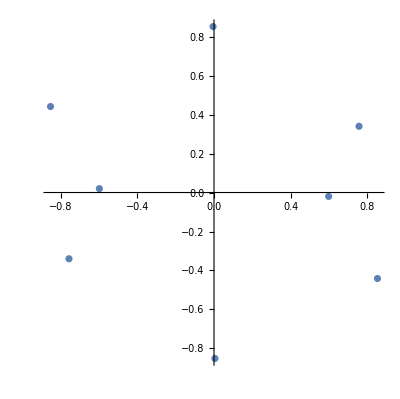

```mathematica
ComplexListPlot[{-2.55614209843521*^10+1.322657396655884*^10 ⅈ,-2.2678412625811974*^10-1.0190157571328022*^10 ⅈ,-1.7925569436129105*^10+5.951779268981696*^8 ⅈ,-1.4855970463246068*^8+2.5519073971985687*^10 ⅈ,1.4855970463245994*^8-2.5519073971985687*^10 ⅈ,1.79255694361291*^10-5.951779268981694*^8 ⅈ,2.2678412625811974*^10+1.0190157571328022*^10 ⅈ,2.55614209843521*^10-1.3226573966558842*^10 ⅈ}/(2.997925*10^10)]
```

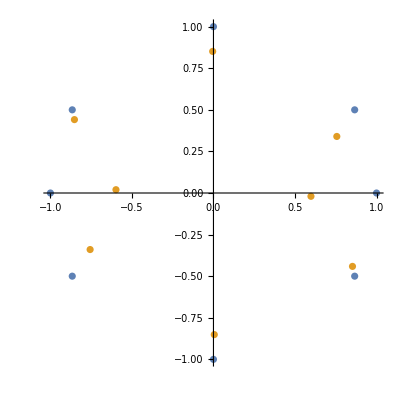

```mathematica
ComplexListPlot[{{-2.997925*^10,-2.5962792086404633*^10-1.4989625*^10 ⅈ,-2.5962792086404633*^10+1.4989625*^10 ⅈ,0.-2.997925*^10 ⅈ,0.+2.997925*^10 ⅈ,2.5962792086404633*^10+1.4989624999999998*^10 ⅈ,2.5962792086404633*^10-1.4989625*^10 ⅈ,2.9979249999999996*^10}/(2.997925*10^10),{-2.55614209843521*^10+1.322657396655884*^10 ⅈ,-2.2678412625811974*^10-1.0190157571328022*^10 ⅈ,-1.7925569436129105*^10+5.951779268981696*^8 ⅈ,-1.4855970463246068*^8+2.5519073971985687*^10 ⅈ,1.4855970463245994*^8-2.5519073971985687*^10 ⅈ,1.79255694361291*^10-5.951779268981694*^8 ⅈ,2.2678412625811974*^10+1.0190157571328022*^10 ⅈ,2.55614209843521*^10-1.3226573966558842*^10 ⅈ}/(2.997925*10^10)}]
```

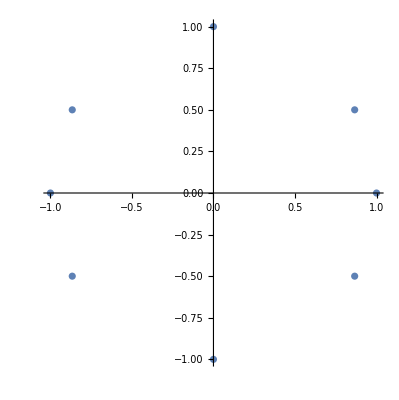

```mathematica
ComplexListPlot[{-0.9999999999999999,-0.8660254037844386-0.49999999999999994 ⅈ,-0.8660254037844386+0.49999999999999994 ⅈ,0.-0.9999999999999999 ⅈ,0.+0.9999999999999999 ⅈ,0.8660254037844386+0.4999999999999999 ⅈ,0.8660254037844386-0.49999999999999994 ⅈ,0.9999999999999998}]
```

```mathematica
(*Einstein tensor:Einstein gravity*)
```

```mathematica
Gij=FullSimplify[wb-gij*wd/2]
```

{{2.93209×10^104-(3.26239×10^83-4.03881×10^41 ⅈ) r^2+(4.49378×10^20+4.03881×10^41 ⅈ) r^4+(4.03881×10^41+4.49378×10^20 ⅈ) r^6-4.49378×10^20 r^8+r^2 (-6.52478×10^83+(0.+4.03881×10^41 ⅈ) r^2+(8.07761×10^41+0.5 ⅈ) r^4-(8.98755×10^20+0.5 ⅈ) r^6) Sin[t0]^2+r^4 ((-0.5-4.03881×10^41 ⅈ)+(4.49378×10^20-4.03881×10^41 ⅈ) r^2-(0.+4.49378×10^20 ⅈ) r^4+(0.+0.5 ⅈ) r^6) Sin[t0]^4+r^6 ((4.03881×10^41-4.49378×10^20 ⅈ)-4.49378×10^20 r^2-(0.+0.5 ⅈ) r^4) Sin[t0]^6-(8.98755×10^20-0.5 ⅈ) r^8 Sin[t0]^8,r^6-ⅈ r^4 Sin[t0]^2,r^2 Sin[t0]^2 (1-ⅈ r^2+r^4 Sin[t0]^2 (1-ⅈ Sin[t0]^2)),8.07761×10^41-(8.07761×10^41-8.98755×10^20 ⅈ) r^2+(0.+8.98755×10^20 ⅈ) r^4 Sin[t0]^2},{r^4+(0.+1. ⅈ) r^2 Sin[t0]^2,r^2 (2.93209×10^104-(3.26239×10^83-4.03881×10^41 ⅈ) r^2+(4.49378×10^20+4.03881×10^41 ⅈ) r^4+(4.03881×10^41+4.49378×10^20 ⅈ) r^6-4.49378×10^20 r^8+r^2 (-6.52478×10^83+(0.+4.03881×10^41 ⅈ) r^2+(8.07761×10^41+0.5 ⅈ) r^4-(8.98755×10^20+0.5 ⅈ) r^6) Sin[t0]^2+r^4 ((-0.5-4.03881×10^41 ⅈ)+(4.49378×10^20-4.03881×10^41 ⅈ) r^2-(0.+4.49378×10^20 ⅈ) r^4+(0.+0.5 ⅈ) r^6) Sin[t0]^4+r^6 ((4.03881×10^41-4.49378×10^20 ⅈ)-4.49378×10^20 r^2-(0.+0.5 ⅈ) r^4) Sin[t0]^6-(8.98755×10^20-0.5 ⅈ) r^8 Sin[t0]^8),r^2 Sin[t0]^2 (-8.98755×10^20-(8.98755×10^20+1. ⅈ) r^2+ⅈ r^4 Sin[t0]^2),-8.98755×10^20+(0.+8.98755×10^20 ⅈ) r^2+r^4 Sin[t0]^2 (8.98755×10^20-(0.+8.98755×10^20 ⅈ) Sin[t0]^2)},{1.+ⅈ r^2+r^4 Sin[t0]^2 (1+ⅈ Sin[t0]^2),-8.98755×10^20 r^2-(8.98755×10^20-1. ⅈ) r^4-ⅈ r^6 Sin[t0]^2,r^2 Sin[t0]^2 (2.93209×10^104-(3.26239×10^83-4.03881×10^41 ⅈ) r^2+(4.49378×10^20+4.03881×10^41 ⅈ) r^4+(4.03881×10^41+4.49378×10^20 ⅈ) r^6-4.49378×10^20 r^8+r^2 (-6.52478×10^83+(0.+4.03881×10^41 ⅈ) r^2+(8.07761×10^41+0.5 ⅈ) r^4-(8.98755×10^20+0.5 ⅈ) r^6) Sin[t0]^2+r^4 ((-0.5-4.03881×10^41 ⅈ)+(4.49378×10^20-4.03881×10^41 ⅈ) r^2-(0.+4.49378×10^20 ⅈ) r^4+(0.+0.5 ⅈ) r^6) Sin[t0]^4+r^6 ((4.03881×10^41-4.49378×10^20 ⅈ)-4.49378×10^20 r^2-(0.+0.5 ⅈ) r^4) Sin[t0]^6-(8.98755×10^20-0.5 ⅈ) r^8 Sin[t0]^8),8.98755×10^20 r^4-(0.+8.98755×10^20 ⅈ) r^2 Sin[t0]^2},{-8.98755×10^20+(8.98755×10^20+1. ⅈ) r^2+ⅈ r^4 Sin[t0]^2,r^2+ⅈ r^4+r^6 Sin[t0]^2 (-1-ⅈ Sin[t0]^2),-r^4 Sin[t0]^2 (r^2+ⅈ Sin[t0]^2),-2.63523×10^125+(2.93209×10^104-3.6299×10^62 ⅈ) r^2-(4.03881×10^41+3.6299×10^62 ⅈ) r^4-(3.6299×10^62+4.03881×10^41 ⅈ) r^6+4.03881×10^41 r^8+r^2 (5.86418×10^104-(0.+3.6299×10^62 ⅈ) r^2-(7.2598×10^62+4.49378×10^20 ⅈ) r^4+(8.07761×10^41+4.49378×10^20 ⅈ) r^6) Sin[t0]^2+r^4 ((4.49378×10^20+3.6299×10^62 ⅈ)-(4.03881×10^41-3.6299×10^62 ⅈ) r^2+(0.+4.03881×10^41 ⅈ) r^4-(0.+4.49378×10^20 ⅈ) r^6) Sin[t0]^4+r^6 ((-3.6299×10^62+4.03881×10^41 ⅈ)+4.03881×10^41 r^2+(0.+4.49378×10^20 ⅈ) r^4) Sin[t0]^6+(8.07761×10^41-4.49378×10^20 ⅈ) r^8 Sin[t0]^8}}

```mathematica
g=Table[Abs[Det[Gij]]/.r->c,{t0,-Pi,Pi,Pi/4}]
```

{0.,5.305547731969×10^480,2.1463233096438×10^483,5.305547731969×10^480,0.,5.305547731969×10^480,2.1463233096438×10^483,5.305547731969×10^480,0.}

```mathematica
G=6.67259*10^(-8);
```

```mathematica
Table[m/.Solve[g[[i]]==(-8*I*G/c^4)*m*c^2/((4*Pi/3)*c^3),m][[1]],{i,Length[g]}]
```

{0.+0. ⅈ,0.+1.00818034633938×10^540 ⅈ,0.+4.07852513442578×10^542 ⅈ,0.+1.00818034633938×10^540 ⅈ,0.+0. ⅈ,0.+1.00818034633938×10^540 ⅈ,0.+4.07852513442578×10^542 ⅈ,0.+1.00818034633938×10^540 ⅈ,0.+0. ⅈ}

```mathematica
gt=Table[Abs[Tr[Gij]]/.r->c,{t0,-Pi,Pi,Pi/4}]
```

{3.75767×10^109,1.5625×10^125,1.17851×10^126,1.5625×10^125,3.75767×10^109,1.5625×10^125,1.17851×10^126,1.5625×10^125,3.75767×10^109}

```mathematica
(Table[(m/.Solve[g[[i]]==(-8*I*G/c^4)*m*c^2/((4*Pi/3)*c^3),m][[1]])/(m/.Solve[gt[[i]]==(-8*I*G/c^4)*m*c^2/((4*Pi/3)*c^3),m][[1]]),{i,Length[gt]}]//Chop)/(3.395547298773163806048405893`15.954589770191005*^355)
```

{0,1.,53.635358810002,1.,0,1.,53.635358810002,1.,0}

```mathematica
Table[m/.Solve[gt[[i]]==(-8*I*G/c^4)*m*c^2/((4*Pi/3)*c^3),m][[1]],{i,Length[gt]}]
```

```mathematica
1/2 c^2 (-c^10+r^6+r^8+c^6 (-1+r^2)+c^8 (1+r^2)-c^4 r^2 (ⅈ+ⅈ r^2+r^4)+c^2 (1+(1-ⅈ) r^2-r^4+(1-ⅈ) r^6+r^8)+r^2 (4+2 c^2+c^6+2 c^8-ⅈ (-2+c^2+c^4) r^2-(ⅈ+c^2+2 c^4) r^4+((1+ⅈ)+2 c^2) r^6) Sin[t0]^2-ⅈ r^4 (ⅈ+(1+ⅈ) r^2+r^4+r^6-c^2 r^2 (ⅈ+r^2)-c^4 (1+r^2)) Sin[t0]^4+r^6 (ⅈ-c^4+r^2+ⅈ r^4+c^2 ((1+ⅈ)+r^2)) Sin[t0]^6+(1+ⅈ) (-1+(1-ⅈ) c^2) r^8 Sin[t0]^8) (1/2 r^2 Sin[t0]^2 (c^10-c^6 (-1+r^2)-c^8 (1+r^2)-r^6 (1+r^2)+c^4 (-4+ⅈ r^2+ⅈ r^4+r^6)+c^2 (3+(3+ⅈ) r^2+r^4-(1-ⅈ) r^6-r^8)+r^2 (-4+6 c^2-c^6-2 c^8+ⅈ (-2+c^2+c^4) r^2+(ⅈ+c^2+2 c^4) r^4+(1+ⅈ) (-1-(1-ⅈ) c^2) r^6) Sin[t0]^2+ⅈ r^4 (ⅈ+(1+ⅈ) r^2+r^4+r^6-c^2 r^2 (ⅈ+r^2)-c^4 (1+r^2)) Sin[t0]^4+r^6 (c^4-c^2 ((1+ⅈ)+r^2)-ⅈ (1-ⅈ r^2+r^4)) Sin[t0]^6+(1+ⅈ) (1-(1-ⅈ) c^2) r^8 Sin[t0]^8) (-((r^4+ⅈ r^2 Sin[t0]^2) (r^6-ⅈ r^4 Sin[t0]^2))+1/4 r^2 (c^10-c^6 (-1+r^2)-c^8 (1+r^2)-r^6 (1+r^2)+c^4 (-4+ⅈ r^2+ⅈ r^4+r^6)+c^2 (3+(3+ⅈ) r^2+r^4-(1-ⅈ) r^6-r^8)+r^2 (-c^2 (-6+c^4+2 c^6)+ⅈ (-2+c^2+c^4) r^2+(ⅈ+c^2+2 c^4) r^4+(1+ⅈ) (-1-(1-ⅈ) c^2) r^6) Sin[t0]^2+ⅈ r^4 (ⅈ+(1+ⅈ) r^2+r^4+r^6-c^2 r^2 (ⅈ+r^2)-c^4 (1+r^2)) Sin[t0]^4+r^6 (c^4-c^2 ((1+ⅈ)+r^2)-ⅈ (1-ⅈ r^2+r^4)) Sin[t0]^6+(1+ⅈ) (1-(1-ⅈ) c^2) r^8 Sin[t0]^8) (c^10-c^6 (-1+r^2)-c^8 (1+r^2)-r^6 (1+r^2)+c^4 r^2 (ⅈ+ⅈ r^2+r^4)+c^2 (-1-(1-ⅈ) r^2+r^4-(1-ⅈ) r^6-r^8)+r^2 (-c^2 (2+c^4+2 c^6)+ⅈ (-2+c^2+c^4) r^2+(ⅈ+c^2+2 c^4) r^4+(1+ⅈ) (-1-(1-ⅈ) c^2) r^6) Sin[t0]^2+ⅈ r^4 (ⅈ+(1+ⅈ) r^2+r^4+r^6-c^2 r^2 (ⅈ+r^2)-c^4 (1+r^2)) Sin[t0]^4+r^6 (c^4-c^2 ((1+ⅈ)+r^2)-ⅈ (1-ⅈ r^2+r^4)) Sin[t0]^6+(1+ⅈ) (1-(1-ⅈ) c^2) r^8 Sin[t0]^8))-(ⅈ r^4-c^2 (r^2+r^4)-ⅈ r^6 Sin[t0]^2) (1/2 ⅈ r^2 Sin[t0]^2 (-r^2+ⅈ c^2 (1+r^2)+r^4 Sin[t0]^2) (c^10-c^6 (-1+r^2)-c^8 (1+r^2)-r^6 (1+r^2)+c^4 r^2 (ⅈ+ⅈ r^2+r^4)+c^2 (-1-(1-ⅈ) r^2+r^4-(1-ⅈ) r^6-r^8)+r^2 (-c^2 (2+c^4+2 c^6)+ⅈ (-2+c^2+c^4) r^2+(ⅈ+c^2+2 c^4) r^4+(1+ⅈ) (-1-(1-ⅈ) c^2) r^6) Sin[t0]^2+ⅈ r^4 (ⅈ+(1+ⅈ) r^2+r^4+r^6-c^2 r^2 (ⅈ+r^2)-c^4 (1+r^2)) Sin[t0]^4+r^6 (c^4-c^2 ((1+ⅈ)+r^2)-ⅈ (1-ⅈ r^2+r^4)) Sin[t0]^6+(1+ⅈ) (1-(1-ⅈ) c^2) r^8 Sin[t0]^8)-r^2 Sin[t0]^2 (r^4+ⅈ r^2 Sin[t0]^2) (1-ⅈ r^2+r^4 Sin[t0]^2 (1-ⅈ Sin[t0]^2)))+(1+ⅈ r^2+r^4 Sin[t0]^2 (1+ⅈ Sin[t0]^2)) (ⅈ r^2 Sin[t0]^2 (r^6-ⅈ r^4 Sin[t0]^2) (-r^2+ⅈ c^2 (1+r^2)+r^4 Sin[t0]^2)-1/2 r^4 Sin[t0]^2 (c^10-c^6 (-1+r^2)-c^8 (1+r^2)-r^6 (1+r^2)+c^4 (-4+ⅈ r^2+ⅈ r^4+r^6)+c^2 (3+(3+ⅈ) r^2+r^4-(1-ⅈ) r^6-r^8)+r^2 (-c^2 (-6+c^4+2 c^6)+ⅈ (-2+c^2+c^4) r^2+(ⅈ+c^2+2 c^4) r^4+(1+ⅈ) (-1-(1-ⅈ) c^2) r^6) Sin[t0]^2+ⅈ r^4 (ⅈ+(1+ⅈ) r^2+r^4+r^6-c^2 r^2 (ⅈ+r^2)-c^4 (1+r^2)) Sin[t0]^4+r^6 (c^4-c^2 ((1+ⅈ)+r^2)-ⅈ (1-ⅈ r^2+r^4)) Sin[t0]^6+(1+ⅈ) (1-(1-ⅈ) c^2) r^8 Sin[t0]^8) (1-ⅈ r^2+r^4 Sin[t0]^2 (1-ⅈ Sin[t0]^2))))+(r^2+ⅈ r^4+r^6 Sin[t0]^2 (-1-ⅈ Sin[t0]^2)) ((-c^2 r^2 Sin[t0]^2+c^6 r^2 Sin[t0]^2+2 ⅈ c^2 r^4 Sin[t0]^2+2 ⅈ c^4 r^4 Sin[t0]^2-c^6 r^6 Sin[t0]^2+2 ⅈ c^4 r^8 Sin[t0]^4+2 c^2 r^10 Sin[t0]^6-2 ⅈ c^2 r^10 Sin[t0]^8-c^2 r^10 Sin[t0]^10) (1+ⅈ r^2+r^4 Sin[t0]^2 (1+ⅈ Sin[t0]^2))+c^2 r^2 (r^2-ⅈ Sin[t0]^2) (1/2 ⅈ r^2 Sin[t0]^2 (-r^2+ⅈ c^2 (1+r^2)+r^4 Sin[t0]^2) (c^10-c^6 (-1+r^2)-c^8 (1+r^2)-r^6 (1+r^2)+c^4 r^2 (ⅈ+ⅈ r^2+r^4)+c^2 (-1-(1-ⅈ) r^2+r^4-(1-ⅈ) r^6-r^8)+r^2 (-c^2 (2+c^4+2 c^6)+ⅈ (-2+c^2+c^4) r^2+(ⅈ+c^2+2 c^4) r^4+(1+ⅈ) (-1-(1-ⅈ) c^2) r^6) Sin[t0]^2+ⅈ r^4 (ⅈ+(1+ⅈ) r^2+r^4+r^6-c^2 r^2 (ⅈ+r^2)-c^4 (1+r^2)) Sin[t0]^4+r^6 (c^4-c^2 ((1+ⅈ)+r^2)-ⅈ (1-ⅈ r^2+r^4)) Sin[t0]^6+(1+ⅈ) (1-(1-ⅈ) c^2) r^8 Sin[t0]^8)-r^2 Sin[t0]^2 (r^4+ⅈ r^2 Sin[t0]^2) (1-ⅈ r^2+r^4 Sin[t0]^2 (1-ⅈ Sin[t0]^2)))-1/2 r^2 Sin[t0]^2 (c^10-c^6 (-1+r^2)-c^8 (1+r^2)-r^6 (1+r^2)+c^4 (-4+ⅈ r^2+ⅈ r^4+r^6)+c^2 (3+(3+ⅈ) r^2+r^4-(1-ⅈ) r^6-r^8)+r^2 (-4+6 c^2-c^6-2 c^8+ⅈ (-2+c^2+c^4) r^2+(ⅈ+c^2+2 c^4) r^4+(1+ⅈ) (-1-(1-ⅈ) c^2) r^6) Sin[t0]^2+ⅈ r^4 (ⅈ+(1+ⅈ) r^2+r^4+r^6-c^2 r^2 (ⅈ+r^2)-c^4 (1+r^2)) Sin[t0]^4+r^6 (c^4-c^2 ((1+ⅈ)+r^2)-ⅈ (1-ⅈ r^2+r^4)) Sin[t0]^6+(1+ⅈ) (1-(1-ⅈ) c^2) r^8 Sin[t0]^8) (1/2 c^2 (c^10-c^6 (-1+r^2)-c^8 (1+r^2)-r^6 (1+r^2)+c^4 r^2 (ⅈ+ⅈ r^2+r^4)+c^2 (-1-(1-ⅈ) r^2+r^4-(1-ⅈ) r^6-r^8)+r^2 (-c^2 (2+c^4+2 c^6)+ⅈ (-2+c^2+c^4) r^2+(ⅈ+c^2+2 c^4) r^4+(1+ⅈ) (-1-(1-ⅈ) c^2) r^6) Sin[t0]^2+ⅈ r^4 (ⅈ+(1+ⅈ) r^2+r^4+r^6-c^2 r^2 (ⅈ+r^2)-c^4 (1+r^2)) Sin[t0]^4+r^6 (c^4-c^2 ((1+ⅈ)+r^2)-ⅈ (1-ⅈ r^2+r^4)) Sin[t0]^6+(1+ⅈ) (1-(1-ⅈ) c^2) r^8 Sin[t0]^8) (-1+ⅈ r^2+r^4 Sin[t0]^2 (1-ⅈ Sin[t0]^2))-(r^4+ⅈ r^2 Sin[t0]^2) (c^4+ⅈ c^2 r^2 (1+ⅈ c^2+r^2 Sin[t0]^2))))-(ⅈ r^2+c^2 (-1+r^2)+ⅈ r^4 Sin[t0]^2) ((ⅈ r^4-c^2 (r^2+r^4)-ⅈ r^6 Sin[t0]^2) (-c^2 r^2 Sin[t0]^2+c^6 r^2 Sin[t0]^2+2 ⅈ c^2 r^4 Sin[t0]^2+2 ⅈ c^4 r^4 Sin[t0]^2-c^6 r^6 Sin[t0]^2+2 ⅈ c^4 r^8 Sin[t0]^4+2 c^2 r^10 Sin[t0]^6-2 ⅈ c^2 r^10 Sin[t0]^8-c^2 r^10 Sin[t0]^10)+c^2 r^2 (r^2-ⅈ Sin[t0]^2) (ⅈ r^2 Sin[t0]^2 (r^6-ⅈ r^4 Sin[t0]^2) (-r^2+ⅈ c^2 (1+r^2)+r^4 Sin[t0]^2)-1/2 r^4 Sin[t0]^2 (c^10-c^6 (-1+r^2)-c^8 (1+r^2)-r^6 (1+r^2)+c^4 (-4+ⅈ r^2+ⅈ r^4+r^6)+c^2 (3+(3+ⅈ) r^2+r^4-(1-ⅈ) r^6-r^8)+r^2 (-c^2 (-6+c^4+2 c^6)+ⅈ (-2+c^2+c^4) r^2+(ⅈ+c^2+2 c^4) r^4+(1+ⅈ) (-1-(1-ⅈ) c^2) r^6) Sin[t0]^2+ⅈ r^4 (ⅈ+(1+ⅈ) r^2+r^4+r^6-c^2 r^2 (ⅈ+r^2)-c^4 (1+r^2)) Sin[t0]^4+r^6 (c^4-c^2 ((1+ⅈ)+r^2)-ⅈ (1-ⅈ r^2+r^4)) Sin[t0]^6+(1+ⅈ) (1-(1-ⅈ) c^2) r^8 Sin[t0]^8) (1-ⅈ r^2+r^4 Sin[t0]^2 (1-ⅈ Sin[t0]^2)))-1/2 r^2 Sin[t0]^2 (c^10-c^6 (-1+r^2)-c^8 (1+r^2)-r^6 (1+r^2)+c^4 (-4+ⅈ r^2+ⅈ r^4+r^6)+c^2 (3+(3+ⅈ) r^2+r^4-(1-ⅈ) r^6-r^8)+r^2 (-4+6 c^2-c^6-2 c^8+ⅈ (-2+c^2+c^4) r^2+(ⅈ+c^2+2 c^4) r^4+(1+ⅈ) (-1-(1-ⅈ) c^2) r^6) Sin[t0]^2+ⅈ r^4 (ⅈ+(1+ⅈ) r^2+r^4+r^6-c^2 r^2 (ⅈ+r^2)-c^4 (1+r^2)) Sin[t0]^4+r^6 (c^4-c^2 ((1+ⅈ)+r^2)-ⅈ (1-ⅈ r^2+r^4)) Sin[t0]^6+(1+ⅈ) (1-(1-ⅈ) c^2) r^8 Sin[t0]^8) (c^2 (r^6-ⅈ r^4 Sin[t0]^2) (-1+ⅈ r^2+r^4 Sin[t0]^2 (1-ⅈ Sin[t0]^2))-1/2 r^2 (c^10-c^6 (-1+r^2)-c^8 (1+r^2)-r^6 (1+r^2)+c^4 (-4+ⅈ r^2+ⅈ r^4+r^6)+c^2 (3+(3+ⅈ) r^2+r^4-(1-ⅈ) r^6-r^8)+r^2 (-c^2 (-6+c^4+2 c^6)+ⅈ (-2+c^2+c^4) r^2+(ⅈ+c^2+2 c^4) r^4+(1+ⅈ) (-1-(1-ⅈ) c^2) r^6) Sin[t0]^2+ⅈ r^4 (ⅈ+(1+ⅈ) r^2+r^4+r^6-c^2 r^2 (ⅈ+r^2)-c^4 (1+r^2)) Sin[t0]^4+r^6 (c^4-c^2 ((1+ⅈ)+r^2)-ⅈ (1-ⅈ r^2+r^4)) Sin[t0]^6+(1+ⅈ) (1-(1-ⅈ) c^2) r^8 Sin[t0]^8) (c^4+ⅈ c^2 r^2 (1+ⅈ c^2+r^2 Sin[t0]^2))))+r^4 Sin[t0]^2 (r^2+ⅈ Sin[t0]^2) (c^2 r^2 (r^2-ⅈ Sin[t0]^2) (-((r^4+ⅈ r^2 Sin[t0]^2) (r^6-ⅈ r^4 Sin[t0]^2))+1/4 r^2 (c^10-c^6 (-1+r^2)-c^8 (1+r^2)-r^6 (1+r^2)+c^4 (-4+ⅈ r^2+ⅈ r^4+r^6)+c^2 (3+(3+ⅈ) r^2+r^4-(1-ⅈ) r^6-r^8)+r^2 (-c^2 (-6+c^4+2 c^6)+ⅈ (-2+c^2+c^4) r^2+(ⅈ+c^2+2 c^4) r^4+(1+ⅈ) (-1-(1-ⅈ) c^2) r^6) Sin[t0]^2+ⅈ r^4 (ⅈ+(1+ⅈ) r^2+r^4+r^6-c^2 r^2 (ⅈ+r^2)-c^4 (1+r^2)) Sin[t0]^4+r^6 (c^4-c^2 ((1+ⅈ)+r^2)-ⅈ (1-ⅈ r^2+r^4)) Sin[t0]^6+(1+ⅈ) (1-(1-ⅈ) c^2) r^8 Sin[t0]^8) (c^10-c^6 (-1+r^2)-c^8 (1+r^2)-r^6 (1+r^2)+c^4 r^2 (ⅈ+ⅈ r^2+r^4)+c^2 (-1-(1-ⅈ) r^2+r^4-(1-ⅈ) r^6-r^8)+r^2 (-c^2 (2+c^4+2 c^6)+ⅈ (-2+c^2+c^4) r^2+(ⅈ+c^2+2 c^4) r^4+(1+ⅈ) (-1-(1-ⅈ) c^2) r^6) Sin[t0]^2+ⅈ r^4 (ⅈ+(1+ⅈ) r^2+r^4+r^6-c^2 r^2 (ⅈ+r^2)-c^4 (1+r^2)) Sin[t0]^4+r^6 (c^4-c^2 ((1+ⅈ)+r^2)-ⅈ (1-ⅈ r^2+r^4)) Sin[t0]^6+(1+ⅈ) (1-(1-ⅈ) c^2) r^8 Sin[t0]^8))-(ⅈ r^4-c^2 (r^2+r^4)-ⅈ r^6 Sin[t0]^2) (1/2 c^2 (c^10-c^6 (-1+r^2)-c^8 (1+r^2)-r^6 (1+r^2)+c^4 r^2 (ⅈ+ⅈ r^2+r^4)+c^2 (-1-(1-ⅈ) r^2+r^4-(1-ⅈ) r^6-r^8)+r^2 (-c^2 (2+c^4+2 c^6)+ⅈ (-2+c^2+c^4) r^2+(ⅈ+c^2+2 c^4) r^4+(1+ⅈ) (-1-(1-ⅈ) c^2) r^6) Sin[t0]^2+ⅈ r^4 (ⅈ+(1+ⅈ) r^2+r^4+r^6-c^2 r^2 (ⅈ+r^2)-c^4 (1+r^2)) Sin[t0]^4+r^6 (c^4-c^2 ((1+ⅈ)+r^2)-ⅈ (1-ⅈ r^2+r^4)) Sin[t0]^6+(1+ⅈ) (1-(1-ⅈ) c^2) r^8 Sin[t0]^8) (-1+ⅈ r^2+r^4 Sin[t0]^2 (1-ⅈ Sin[t0]^2))-(r^4+ⅈ r^2 Sin[t0]^2) (c^4+ⅈ c^2 r^2 (1+ⅈ c^2+r^2 Sin[t0]^2)))+(1+ⅈ r^2+r^4 Sin[t0]^2 (1+ⅈ Sin[t0]^2)) (c^2 (r^6-ⅈ r^4 Sin[t0]^2) (-1+ⅈ r^2+r^4 Sin[t0]^2 (1-ⅈ Sin[t0]^2))-1/2 r^2 (c^10-c^6 (-1+r^2)-c^8 (1+r^2)-r^6 (1+r^2)+c^4 (-4+ⅈ r^2+ⅈ r^4+r^6)+c^2 (3+(3+ⅈ) r^2+r^4-(1-ⅈ) r^6-r^8)+r^2 (-c^2 (-6+c^4+2 c^6)+ⅈ (-2+c^2+c^4) r^2+(ⅈ+c^2+2 c^4) r^4+(1+ⅈ) (-1-(1-ⅈ) c^2) r^6) Sin[t0]^2+ⅈ r^4 (ⅈ+(1+ⅈ) r^2+r^4+r^6-c^2 r^2 (ⅈ+r^2)-c^4 (1+r^2)) Sin[t0]^4+r^6 (c^4-c^2 ((1+ⅈ)+r^2)-ⅈ (1-ⅈ r^2+r^4)) Sin[t0]^6+(1+ⅈ) (1-(1-ⅈ) c^2) r^8 Sin[t0]^8) (c^4+ⅈ c^2 r^2 (1+ⅈ c^2+r^2 Sin[t0]^2))))/.t0->Pi/2/.c->2.997925*10^10
```

(r^2+ⅈ r^4-(1+ⅈ) r^6) ((1+ⅈ r^2+(1+ⅈ) r^4) (7.2598×10^62 r^2+(0.+1.61552×10^42 ⅈ) r^4-7.2598×10^62 r^6+(0.+1.61552×10^42 ⅈ) r^8+(8.98755×10^20-1.79751×10^21 ⅈ) r^10)-1/2 r^2 (5.86418×10^104-(1.79751×10^21+0. ⅈ) r^8-7.2598×10^62 (-1+r^2)-6.52478×10^83 (1+r^2)-r^6 (1+r^2)+r^2 (-1.30496×10^84+(0.+8.07761×10^41 ⅈ) r^2+(1.61552×10^42+1. ⅈ) r^4-(1.79751×10^21+0. ⅈ) r^6)+8.07761×10^41 (-4+ⅈ r^2+ⅈ r^4+r^6)+8.98755×10^20 (3+(3+ⅈ) r^2+r^4-(1-ⅈ) r^6-r^8)+ⅈ r^4 (ⅈ+(1+ⅈ) r^2+r^4+r^6-8.98755×10^20 r^2 (ⅈ+r^2)-8.07761×10^41 (1+r^2))+r^6 (8.07761×10^41-8.98755×10^20 ((1+ⅈ)+r^2)-ⅈ (1-ⅈ r^2+r^4))) (-((ⅈ r^2+r^4) (8.07761×10^41+(0.+8.98755×10^20 ⅈ) r^2 ((1.+8.98755×10^20 ⅈ)+r^2)))+4.49378×10^20 (-1+ⅈ r^2+(1-ⅈ) r^4) (5.86418×10^104-(1.79751×10^21+0. ⅈ) r^8-7.2598×10^62 (-1+r^2)-6.52478×10^83 (1+r^2)-r^6 (1+r^2)+8.07761×10^41 r^2 (ⅈ+ⅈ r^2+r^4)+r^2 (-1.30496×10^84+(0.+8.07761×10^41 ⅈ) r^2+(1.61552×10^42+1. ⅈ) r^4-(1.79751×10^21+0. ⅈ) r^6)+8.98755×10^20 (-1-(1-ⅈ) r^2+r^4-(1-ⅈ) r^6-r^8)+ⅈ r^4 (ⅈ+(1+ⅈ) r^2+r^4+r^6-8.98755×10^20 r^2 (ⅈ+r^2)-8.07761×10^41 (1+r^2))+r^6 (8.07761×10^41-8.98755×10^20 ((1+ⅈ)+r^2)-ⅈ (1-ⅈ r^2+r^4))))+8.98755×10^20 r^2 (-ⅈ+r^2) (-r^2 (ⅈ r^2+r^4) (1-ⅈ r^2+(1-ⅈ) r^4)+1/2 ⅈ r^2 (-r^2+r^4+(0.+8.98755×10^20 ⅈ) (1+r^2)) (5.86418×10^104-(1.79751×10^21+0. ⅈ) r^8-7.2598×10^62 (-1+r^2)-6.52478×10^83 (1+r^2)-r^6 (1+r^2)+8.07761×10^41 r^2 (ⅈ+ⅈ r^2+r^4)+r^2 (-1.30496×10^84+(0.+8.07761×10^41 ⅈ) r^2+(1.61552×10^42+1. ⅈ) r^4-(1.79751×10^21+0. ⅈ) r^6)+8.98755×10^20 (-1-(1-ⅈ) r^2+r^4-(1-ⅈ) r^6-r^8)+ⅈ r^4 (ⅈ+(1+ⅈ) r^2+r^4+r^6-8.98755×10^20 r^2 (ⅈ+r^2)-8.07761×10^41 (1+r^2))+r^6 (8.07761×10^41-8.98755×10^20 ((1+ⅈ)+r^2)-ⅈ (1-ⅈ r^2+r^4)))))-(ⅈ r^2+ⅈ r^4+8.98755×10^20 (-1+r^2)) ((7.2598×10^62 r^2+(0.+1.61552×10^42 ⅈ) r^4-7.2598×10^62 r^6+(0.+1.61552×10^42 ⅈ) r^8+(8.98755×10^20-1.79751×10^21 ⅈ) r^10) (ⅈ r^4-ⅈ r^6-8.98755×10^20 (r^2+r^4))+8.98755×10^20 r^2 (-ⅈ+r^2) (ⅈ r^2 (-ⅈ r^4+r^6) (-r^2+r^4+(0.+8.98755×10^20 ⅈ) (1+r^2))-1/2 r^4 (1-ⅈ r^2+(1-ⅈ) r^4) (5.86418×10^104-(1.79751×10^21+0. ⅈ) r^8-7.2598×10^62 (-1+r^2)-6.52478×10^83 (1+r^2)-r^6 (1+r^2)+r^2 (-1.30496×10^84+(0.+8.07761×10^41 ⅈ) r^2+(1.61552×10^42+1. ⅈ) r^4-(1.79751×10^21+0. ⅈ) r^6)+8.07761×10^41 (-4+ⅈ r^2+ⅈ r^4+r^6)+8.98755×10^20 (3+(3+ⅈ) r^2+r^4-(1-ⅈ) r^6-r^8)+ⅈ r^4 (ⅈ+(1+ⅈ) r^2+r^4+r^6-8.98755×10^20 r^2 (ⅈ+r^2)-8.07761×10^41 (1+r^2))+r^6 (8.07761×10^41-8.98755×10^20 ((1+ⅈ)+r^2)-ⅈ (1-ⅈ r^2+r^4))))-1/2 r^2 (5.86418×10^104-(1.79751×10^21+0. ⅈ) r^8-7.2598×10^62 (-1+r^2)-6.52478×10^83 (1+r^2)-r^6 (1+r^2)+r^2 (-1.30496×10^84+(0.+8.07761×10^41 ⅈ) r^2+(1.61552×10^42+1. ⅈ) r^4-(1.79751×10^21+0. ⅈ) r^6)+8.07761×10^41 (-4+ⅈ r^2+ⅈ r^4+r^6)+8.98755×10^20 (3+(3+ⅈ) r^2+r^4-(1-ⅈ) r^6-r^8)+ⅈ r^4 (ⅈ+(1+ⅈ) r^2+r^4+r^6-8.98755×10^20 r^2 (ⅈ+r^2)-8.07761×10^41 (1+r^2))+r^6 (8.07761×10^41-8.98755×10^20 ((1+ⅈ)+r^2)-ⅈ (1-ⅈ r^2+r^4))) (8.98755×10^20 (-1+ⅈ r^2+(1-ⅈ) r^4) (-ⅈ r^4+r^6)-1/2 r^2 (8.07761×10^41+(0.+8.98755×10^20 ⅈ) r^2 ((1.+8.98755×10^20 ⅈ)+r^2)) (5.86418×10^104-(1.79751×10^21+0. ⅈ) r^8-7.2598×10^62 (-1+r^2)-6.52478×10^83 (1+r^2)-r^6 (1+r^2)+r^2 (-1.30496×10^84+(0.+8.07761×10^41 ⅈ) r^2+(1.61552×10^42+1. ⅈ) r^4-(1.79751×10^21+0. ⅈ) r^6)+8.07761×10^41 (-4+ⅈ r^2+ⅈ r^4+r^6)+8.98755×10^20 (3+(3+ⅈ) r^2+r^4-(1-ⅈ) r^6-r^8)+ⅈ r^4 (ⅈ+(1+ⅈ) r^2+r^4+r^6-8.98755×10^20 r^2 (ⅈ+r^2)-8.07761×10^41 (1+r^2))+r^6 (8.07761×10^41-8.98755×10^20 ((1+ⅈ)+r^2)-ⅈ (1-ⅈ r^2+r^4)))))+r^4 (ⅈ+r^2) (-((ⅈ r^4-ⅈ r^6-8.98755×10^20 (r^2+r^4)) (-((ⅈ r^2+r^4) (8.07761×10^41+(0.+8.98755×10^20 ⅈ) r^2 ((1.+8.98755×10^20 ⅈ)+r^2)))+4.49378×10^20 (-1+ⅈ r^2+(1-ⅈ) r^4) (5.86418×10^104-(1.79751×10^21+0. ⅈ) r^8-7.2598×10^62 (-1+r^2)-6.52478×10^83 (1+r^2)-r^6 (1+r^2)+8.07761×10^41 r^2 (ⅈ+ⅈ r^2+r^4)+r^2 (-1.30496×10^84+(0.+8.07761×10^41 ⅈ) r^2+(1.61552×10^42+1. ⅈ) r^4-(1.79751×10^21+0. ⅈ) r^6)+8.98755×10^20 (-1-(1-ⅈ) r^2+r^4-(1-ⅈ) r^6-r^8)+ⅈ r^4 (ⅈ+(1+ⅈ) r^2+r^4+r^6-8.98755×10^20 r^2 (ⅈ+r^2)-8.07761×10^41 (1+r^2))+r^6 (8.07761×10^41-8.98755×10^20 ((1+ⅈ)+r^2)-ⅈ (1-ⅈ r^2+r^4)))))+(1+ⅈ r^2+(1+ⅈ) r^4) (8.98755×10^20 (-1+ⅈ r^2+(1-ⅈ) r^4) (-ⅈ r^4+r^6)-1/2 r^2 (8.07761×10^41+(0.+8.98755×10^20 ⅈ) r^2 ((1.+8.98755×10^20 ⅈ)+r^2)) (5.86418×10^104-(1.79751×10^21+0. ⅈ) r^8-7.2598×10^62 (-1+r^2)-6.52478×10^83 (1+r^2)-r^6 (1+r^2)+r^2 (-1.30496×10^84+(0.+8.07761×10^41 ⅈ) r^2+(1.61552×10^42+1. ⅈ) r^4-(1.79751×10^21+0. ⅈ) r^6)+8.07761×10^41 (-4+ⅈ r^2+ⅈ r^4+r^6)+8.98755×10^20 (3+(3+ⅈ) r^2+r^4-(1-ⅈ) r^6-r^8)+ⅈ r^4 (ⅈ+(1+ⅈ) r^2+r^4+r^6-8.98755×10^20 r^2 (ⅈ+r^2)-8.07761×10^41 (1+r^2))+r^6 (8.07761×10^41-8.98755×10^20 ((1+ⅈ)+r^2)-ⅈ (1-ⅈ r^2+r^4))))+8.98755×10^20 r^2 (-ⅈ+r^2) (-((ⅈ r^2+r^4) (-ⅈ r^4+r^6))+1/4 r^2 (5.86418×10^104-(1.79751×10^21+0. ⅈ) r^8-7.2598×10^62 (-1+r^2)-6.52478×10^83 (1+r^2)-r^6 (1+r^2)+8.07761×10^41 r^2 (ⅈ+ⅈ r^2+r^4)+r^2 (-1.30496×10^84+(0.+8.07761×10^41 ⅈ) r^2+(1.61552×10^42+1. ⅈ) r^4-(1.79751×10^21+0. ⅈ) r^6)+8.98755×10^20 (-1-(1-ⅈ) r^2+r^4-(1-ⅈ) r^6-r^8)+ⅈ r^4 (ⅈ+(1+ⅈ) r^2+r^4+r^6-8.98755×10^20 r^2 (ⅈ+r^2)-8.07761×10^41 (1+r^2))+r^6 (8.07761×10^41-8.98755×10^20 ((1+ⅈ)+r^2)-ⅈ (1-ⅈ r^2+r^4))) (5.86418×10^104-(1.79751×10^21+0. ⅈ) r^8-7.2598×10^62 (-1+r^2)-6.52478×10^83 (1+r^2)-r^6 (1+r^2)+r^2 (-1.30496×10^84+(0.+8.07761×10^41 ⅈ) r^2+(1.61552×10^42+1. ⅈ) r^4-(1.79751×10^21+0. ⅈ) r^6)+8.07761×10^41 (-4+ⅈ r^2+ⅈ r^4+r^6)+8.98755×10^20 (3+(3+ⅈ) r^2+r^4-(1-ⅈ) r^6-r^8)+ⅈ r^4 (ⅈ+(1+ⅈ) r^2+r^4+r^6-8.98755×10^20 r^2 (ⅈ+r^2)-8.07761×10^41 (1+r^2))+r^6 (8.07761×10^41-8.98755×10^20 ((1+ⅈ)+r^2)-ⅈ (1-ⅈ r^2+r^4)))))+4.49378×10^20 (-5.86418×10^104+r^6+(1.79751×10^21+0. ⅈ) r^8+7.2598×10^62 (-1+r^2)+6.52478×10^83 (1+r^2)-8.07761×10^41 r^2 (ⅈ+ⅈ r^2+r^4)+r^2 (1.30496×10^84-(0.+8.07761×10^41 ⅈ) r^2-(1.61552×10^42+1. ⅈ) r^4+(1.79751×10^21+1. ⅈ) r^6)+8.98755×10^20 (1+(1-ⅈ) r^2-r^4+(1-ⅈ) r^6+r^8)-ⅈ r^4 (ⅈ+(1+ⅈ) r^2+r^4+r^6-8.98755×10^20 r^2 (ⅈ+r^2)-8.07761×10^41 (1+r^2))+r^6 ((-8.07761×10^41+1. ⅈ)+r^2+ⅈ r^4+8.98755×10^20 ((1+ⅈ)+r^2))) (-((ⅈ r^4-ⅈ r^6-8.98755×10^20 (r^2+r^4)) (-r^2 (ⅈ r^2+r^4) (1-ⅈ r^2+(1-ⅈ) r^4)+1/2 ⅈ r^2 (-r^2+r^4+(0.+8.98755×10^20 ⅈ) (1+r^2)) (5.86418×10^104-(1.79751×10^21+0. ⅈ) r^8-7.2598×10^62 (-1+r^2)-6.52478×10^83 (1+r^2)-r^6 (1+r^2)+8.07761×10^41 r^2 (ⅈ+ⅈ r^2+r^4)+r^2 (-1.30496×10^84+(0.+8.07761×10^41 ⅈ) r^2+(1.61552×10^42+1. ⅈ) r^4-(1.79751×10^21+0. ⅈ) r^6)+8.98755×10^20 (-1-(1-ⅈ) r^2+r^4-(1-ⅈ) r^6-r^8)+ⅈ r^4 (ⅈ+(1+ⅈ) r^2+r^4+r^6-8.98755×10^20 r^2 (ⅈ+r^2)-8.07761×10^41 (1+r^2))+r^6 (8.07761×10^41-8.98755×10^20 ((1+ⅈ)+r^2)-ⅈ (1-ⅈ r^2+r^4)))))+(1+ⅈ r^2+(1+ⅈ) r^4) (ⅈ r^2 (-ⅈ r^4+r^6) (-r^2+r^4+(0.+8.98755×10^20 ⅈ) (1+r^2))-1/2 r^4 (1-ⅈ r^2+(1-ⅈ) r^4) (5.86418×10^104-(1.79751×10^21+0. ⅈ) r^8-7.2598×10^62 (-1+r^2)-6.52478×10^83 (1+r^2)-r^6 (1+r^2)+r^2 (-1.30496×10^84+(0.+8.07761×10^41 ⅈ) r^2+(1.61552×10^42+1. ⅈ) r^4-(1.79751×10^21+0. ⅈ) r^6)+8.07761×10^41 (-4+ⅈ r^2+ⅈ r^4+r^6)+8.98755×10^20 (3+(3+ⅈ) r^2+r^4-(1-ⅈ) r^6-r^8)+ⅈ r^4 (ⅈ+(1+ⅈ) r^2+r^4+r^6-8.98755×10^20 r^2 (ⅈ+r^2)-8.07761×10^41 (1+r^2))+r^6 (8.07761×10^41-8.98755×10^20 ((1+ⅈ)+r^2)-ⅈ (1-ⅈ r^2+r^4))))+1/2 r^2 (5.86418×10^104-(1.79751×10^21+0. ⅈ) r^8-7.2598×10^62 (-1+r^2)-6.52478×10^83 (1+r^2)-r^6 (1+r^2)+r^2 (-1.30496×10^84+(0.+8.07761×10^41 ⅈ) r^2+(1.61552×10^42+1. ⅈ) r^4-(1.79751×10^21+0. ⅈ) r^6)+8.07761×10^41 (-4+ⅈ r^2+ⅈ r^4+r^6)+8.98755×10^20 (3+(3+ⅈ) r^2+r^4-(1-ⅈ) r^6-r^8)+ⅈ r^4 (ⅈ+(1+ⅈ) r^2+r^4+r^6-8.98755×10^20 r^2 (ⅈ+r^2)-8.07761×10^41 (1+r^2))+r^6 (8.07761×10^41-8.98755×10^20 ((1+ⅈ)+r^2)-ⅈ (1-ⅈ r^2+r^4))) (-((ⅈ r^2+r^4) (-ⅈ r^4+r^6))+1/4 r^2 (5.86418×10^104-(1.79751×10^21+0. ⅈ) r^8-7.2598×10^62 (-1+r^2)-6.52478×10^83 (1+r^2)-r^6 (1+r^2)+8.07761×10^41 r^2 (ⅈ+ⅈ r^2+r^4)+r^2 (-1.30496×10^84+(0.+8.07761×10^41 ⅈ) r^2+(1.61552×10^42+1. ⅈ) r^4-(1.79751×10^21+0. ⅈ) r^6)+8.98755×10^20 (-1-(1-ⅈ) r^2+r^4-(1-ⅈ) r^6-r^8)+ⅈ r^4 (ⅈ+(1+ⅈ) r^2+r^4+r^6-8.98755×10^20 r^2 (ⅈ+r^2)-8.07761×10^41 (1+r^2))+r^6 (8.07761×10^41-8.98755×10^20 ((1+ⅈ)+r^2)-ⅈ (1-ⅈ r^2+r^4))) (5.86418×10^104-(1.79751×10^21+0. ⅈ) r^8-7.2598×10^62 (-1+r^2)-6.52478×10^83 (1+r^2)-r^6 (1+r^2)+r^2 (-1.30496×10^84+(0.+8.07761×10^41 ⅈ) r^2+(1.61552×10^42+1. ⅈ) r^4-(1.79751×10^21+0. ⅈ) r^6)+8.07761×10^41 (-4+ⅈ r^2+ⅈ r^4+r^6)+8.98755×10^20 (3+(3+ⅈ) r^2+r^4-(1-ⅈ) r^6-r^8)+ⅈ r^4 (ⅈ+(1+ⅈ) r^2+r^4+r^6-8.98755×10^20 r^2 (ⅈ+r^2)-8.07761×10^41 (1+r^2))+r^6 (8.07761×10^41-8.98755×10^20 ((1+ⅈ)+r^2)-ⅈ (1-ⅈ r^2+r^4)))))

```mathematica
r/.Solve[(r^2+ⅈ r^4-(1+ⅈ) r^6) ((1+ⅈ r^2+(1+ⅈ) r^4) (7.259798765124243*^62 r^2+(0.+1.6155226479311698*^42 ⅈ) r^4-7.259798765124243*^62 r^6+(0.+1.6155226479311698*^42 ⅈ) r^8+(8.987554305625*^20-1.797510861125*^21 ⅈ) r^10)-1/2 r^2 (5.864184662240476*^104-(1.797510861125*^21+0. ⅈ) r^8-7.259798765124243*^62 (-1+r^2)-6.524783564946346*^83 (1+r^2)-r^6 (1+r^2)+r^2 (-1.3049567129892693*^84+(0.+8.077613239655849*^41 ⅈ) r^2+(1.6155226479311698*^42+1. ⅈ) r^4-(1.797510861125*^21+0. ⅈ) r^6)+8.077613239655849*^41 (-4+ⅈ r^2+ⅈ r^4+r^6)+8.987554305625*^20 (3+(3+ⅈ) r^2+r^4-(1-ⅈ) r^6-r^8)+ⅈ r^4 (ⅈ+(1+ⅈ) r^2+r^4+r^6-8.987554305625*^20 r^2 (ⅈ+r^2)-8.077613239655849*^41 (1+r^2))+r^6 (8.077613239655849*^41-8.987554305625*^20 ((1+ⅈ)+r^2)-ⅈ (1-ⅈ r^2+r^4))) (-((ⅈ r^2+r^4) (8.077613239655849*^41+(0.+8.987554305625*^20 ⅈ) r^2 ((1.+8.987554305625*^20 ⅈ)+r^2)))+4.4937771528125*^20 (-1+ⅈ r^2+(1-ⅈ) r^4) (5.864184662240476*^104-(1.797510861125*^21+0. ⅈ) r^8-7.259798765124243*^62 (-1+r^2)-6.524783564946346*^83 (1+r^2)-r^6 (1+r^2)+8.077613239655849*^41 r^2 (ⅈ+ⅈ r^2+r^4)+r^2 (-1.304956712989269*^84+(0.+8.077613239655849*^41 ⅈ) r^2+(1.6155226479311698*^42+1. ⅈ) r^4-(1.797510861125*^21+0. ⅈ) r^6)+8.987554305625*^20 (-1-(1-ⅈ) r^2+r^4-(1-ⅈ) r^6-r^8)+ⅈ r^4 (ⅈ+(1+ⅈ) r^2+r^4+r^6-8.987554305625*^20 r^2 (ⅈ+r^2)-8.077613239655849*^41 (1+r^2))+r^6 (8.077613239655849*^41-8.987554305625*^20 ((1+ⅈ)+r^2)-ⅈ (1-ⅈ r^2+r^4))))+8.987554305625*^20 r^2 (-ⅈ+r^2) (-r^2 (ⅈ r^2+r^4) (1-ⅈ r^2+(1-ⅈ) r^4)+1/2 ⅈ r^2 (-r^2+r^4+(0.+8.987554305625*^20 ⅈ) (1+r^2)) (5.864184662240476*^104-(1.797510861125*^21+0. ⅈ) r^8-7.259798765124243*^62 (-1+r^2)-6.524783564946346*^83 (1+r^2)-r^6 (1+r^2)+8.077613239655849*^41 r^2 (ⅈ+ⅈ r^2+r^4)+r^2 (-1.304956712989269*^84+(0.+8.077613239655849*^41 ⅈ) r^2+(1.6155226479311698*^42+1. ⅈ) r^4-(1.797510861125*^21+0. ⅈ) r^6)+8.987554305625*^20 (-1-(1-ⅈ) r^2+r^4-(1-ⅈ) r^6-r^8)+ⅈ r^4 (ⅈ+(1+ⅈ) r^2+r^4+r^6-8.987554305625*^20 r^2 (ⅈ+r^2)-8.077613239655849*^41 (1+r^2))+r^6 (8.077613239655849*^41-8.987554305625*^20 ((1+ⅈ)+r^2)-ⅈ (1-ⅈ r^2+r^4)))))-(ⅈ r^2+ⅈ r^4+8.987554305625*^20 (-1+r^2)) ((7.259798765124243*^62 r^2+(0.+1.6155226479311698*^42 ⅈ) r^4-7.259798765124243*^62 r^6+(0.+1.6155226479311698*^42 ⅈ) r^8+(8.987554305625*^20-1.797510861125*^21 ⅈ) r^10) (ⅈ r^4-ⅈ r^6-8.987554305625*^20 (r^2+r^4))+8.987554305625*^20 r^2 (-ⅈ+r^2) (ⅈ r^2 (-ⅈ r^4+r^6) (-r^2+r^4+(0.+8.987554305625*^20 ⅈ) (1+r^2))-1/2 r^4 (1-ⅈ r^2+(1-ⅈ) r^4) (5.864184662240476*^104-(1.797510861125*^21+0. ⅈ) r^8-7.259798765124243*^62 (-1+r^2)-6.524783564946346*^83 (1+r^2)-r^6 (1+r^2)+r^2 (-1.304956712989269*^84+(0.+8.077613239655849*^41 ⅈ) r^2+(1.6155226479311698*^42+1. ⅈ) r^4-(1.797510861125*^21+0. ⅈ) r^6)+8.077613239655849*^41 (-4+ⅈ r^2+ⅈ r^4+r^6)+8.987554305625*^20 (3+(3+ⅈ) r^2+r^4-(1-ⅈ) r^6-r^8)+ⅈ r^4 (ⅈ+(1+ⅈ) r^2+r^4+r^6-8.987554305625*^20 r^2 (ⅈ+r^2)-8.077613239655849*^41 (1+r^2))+r^6 (8.077613239655849*^41-8.987554305625*^20 ((1+ⅈ)+r^2)-ⅈ (1-ⅈ r^2+r^4))))-1/2 r^2 (5.864184662240476*^104-(1.797510861125*^21+0. ⅈ) r^8-7.259798765124243*^62 (-1+r^2)-6.524783564946346*^83 (1+r^2)-r^6 (1+r^2)+r^2 (-1.3049567129892693*^84+(0.+8.077613239655849*^41 ⅈ) r^2+(1.6155226479311698*^42+1. ⅈ) r^4-(1.797510861125*^21+0. ⅈ) r^6)+8.077613239655849*^41 (-4+ⅈ r^2+ⅈ r^4+r^6)+8.987554305625*^20 (3+(3+ⅈ) r^2+r^4-(1-ⅈ) r^6-r^8)+ⅈ r^4 (ⅈ+(1+ⅈ) r^2+r^4+r^6-8.987554305625*^20 r^2 (ⅈ+r^2)-8.077613239655849*^41 (1+r^2))+r^6 (8.077613239655849*^41-8.987554305625*^20 ((1+ⅈ)+r^2)-ⅈ (1-ⅈ r^2+r^4))) (8.987554305625*^20 (-1+ⅈ r^2+(1-ⅈ) r^4) (-ⅈ r^4+r^6)-1/2 r^2 (8.077613239655849*^41+(0.+8.987554305625*^20 ⅈ) r^2 ((1.+8.987554305625*^20 ⅈ)+r^2)) (5.864184662240476*^104-(1.797510861125*^21+0. ⅈ) r^8-7.259798765124243*^62 (-1+r^2)-6.524783564946346*^83 (1+r^2)-r^6 (1+r^2)+r^2 (-1.304956712989269*^84+(0.+8.077613239655849*^41 ⅈ) r^2+(1.6155226479311698*^42+1. ⅈ) r^4-(1.797510861125*^21+0. ⅈ) r^6)+8.077613239655849*^41 (-4+ⅈ r^2+ⅈ r^4+r^6)+8.987554305625*^20 (3+(3+ⅈ) r^2+r^4-(1-ⅈ) r^6-r^8)+ⅈ r^4 (ⅈ+(1+ⅈ) r^2+r^4+r^6-8.987554305625*^20 r^2 (ⅈ+r^2)-8.077613239655849*^41 (1+r^2))+r^6 (8.077613239655849*^41-8.987554305625*^20 ((1+ⅈ)+r^2)-ⅈ (1-ⅈ r^2+r^4)))))+r^4 (ⅈ+r^2) (-((ⅈ r^4-ⅈ r^6-8.987554305625*^20 (r^2+r^4)) (-((ⅈ r^2+r^4) (8.077613239655849*^41+(0.+8.987554305625*^20 ⅈ) r^2 ((1.+8.987554305625*^20 ⅈ)+r^2)))+4.4937771528125*^20 (-1+ⅈ r^2+(1-ⅈ) r^4) (5.864184662240476*^104-(1.797510861125*^21+0. ⅈ) r^8-7.259798765124243*^62 (-1+r^2)-6.524783564946346*^83 (1+r^2)-r^6 (1+r^2)+8.077613239655849*^41 r^2 (ⅈ+ⅈ r^2+r^4)+r^2 (-1.304956712989269*^84+(0.+8.077613239655849*^41 ⅈ) r^2+(1.6155226479311698*^42+1. ⅈ) r^4-(1.797510861125*^21+0. ⅈ) r^6)+8.987554305625*^20 (-1-(1-ⅈ) r^2+r^4-(1-ⅈ) r^6-r^8)+ⅈ r^4 (ⅈ+(1+ⅈ) r^2+r^4+r^6-8.987554305625*^20 r^2 (ⅈ+r^2)-8.077613239655849*^41 (1+r^2))+r^6 (8.077613239655849*^41-8.987554305625*^20 ((1+ⅈ)+r^2)-ⅈ (1-ⅈ r^2+r^4)))))+(1+ⅈ r^2+(1+ⅈ) r^4) (8.987554305625*^20 (-1+ⅈ r^2+(1-ⅈ) r^4) (-ⅈ r^4+r^6)-1/2 r^2 (8.077613239655849*^41+(0.+8.987554305625*^20 ⅈ) r^2 ((1.+8.987554305625*^20 ⅈ)+r^2)) (5.864184662240476*^104-(1.797510861125*^21+0. ⅈ) r^8-7.259798765124243*^62 (-1+r^2)-6.524783564946346*^83 (1+r^2)-r^6 (1+r^2)+r^2 (-1.304956712989269*^84+(0.+8.077613239655849*^41 ⅈ) r^2+(1.6155226479311698*^42+1. ⅈ) r^4-(1.797510861125*^21+0. ⅈ) r^6)+8.077613239655849*^41 (-4+ⅈ r^2+ⅈ r^4+r^6)+8.987554305625*^20 (3+(3+ⅈ) r^2+r^4-(1-ⅈ) r^6-r^8)+ⅈ r^4 (ⅈ+(1+ⅈ) r^2+r^4+r^6-8.987554305625*^20 r^2 (ⅈ+r^2)-8.077613239655849*^41 (1+r^2))+r^6 (8.077613239655849*^41-8.987554305625*^20 ((1+ⅈ)+r^2)-ⅈ (1-ⅈ r^2+r^4))))+8.987554305625*^20 r^2 (-ⅈ+r^2) (-((ⅈ r^2+r^4) (-ⅈ r^4+r^6))+1/4 r^2 (5.864184662240476*^104-(1.797510861125*^21+0. ⅈ) r^8-7.259798765124243*^62 (-1+r^2)-6.524783564946346*^83 (1+r^2)-r^6 (1+r^2)+8.077613239655849*^41 r^2 (ⅈ+ⅈ r^2+r^4)+r^2 (-1.304956712989269*^84+(0.+8.077613239655849*^41 ⅈ) r^2+(1.6155226479311698*^42+1. ⅈ) r^4-(1.797510861125*^21+0. ⅈ) r^6)+8.987554305625*^20 (-1-(1-ⅈ) r^2+r^4-(1-ⅈ) r^6-r^8)+ⅈ r^4 (ⅈ+(1+ⅈ) r^2+r^4+r^6-8.987554305625*^20 r^2 (ⅈ+r^2)-8.077613239655849*^41 (1+r^2))+r^6 (8.077613239655849*^41-8.987554305625*^20 ((1+ⅈ)+r^2)-ⅈ (1-ⅈ r^2+r^4))) (5.864184662240476*^104-(1.797510861125*^21+0. ⅈ) r^8-7.259798765124243*^62 (-1+r^2)-6.524783564946346*^83 (1+r^2)-r^6 (1+r^2)+r^2 (-1.304956712989269*^84+(0.+8.077613239655849*^41 ⅈ) r^2+(1.6155226479311698*^42+1. ⅈ) r^4-(1.797510861125*^21+0. ⅈ) r^6)+8.077613239655849*^41 (-4+ⅈ r^2+ⅈ r^4+r^6)+8.987554305625*^20 (3+(3+ⅈ) r^2+r^4-(1-ⅈ) r^6-r^8)+ⅈ r^4 (ⅈ+(1+ⅈ) r^2+r^4+r^6-8.987554305625*^20 r^2 (ⅈ+r^2)-8.077613239655849*^41 (1+r^2))+r^6 (8.077613239655849*^41-8.987554305625*^20 ((1+ⅈ)+r^2)-ⅈ (1-ⅈ r^2+r^4)))))+4.4937771528125*^20 (-5.864184662240476*^104+r^6+(1.797510861125*^21+0. ⅈ) r^8+7.259798765124243*^62 (-1+r^2)+6.524783564946346*^83 (1+r^2)-8.077613239655849*^41 r^2 (ⅈ+ⅈ r^2+r^4)+r^2 (1.3049567129892693*^84-(0.+8.077613239655849*^41 ⅈ) r^2-(1.6155226479311698*^42+1. ⅈ) r^4+(1.797510861125*^21+1. ⅈ) r^6)+8.987554305625*^20 (1+(1-ⅈ) r^2-r^4+(1-ⅈ) r^6+r^8)-ⅈ r^4 (ⅈ+(1+ⅈ) r^2+r^4+r^6-8.987554305625*^20 r^2 (ⅈ+r^2)-8.077613239655849*^41 (1+r^2))+r^6 ((-8.077613239655849*^41+1. ⅈ)+r^2+ⅈ r^4+8.987554305625*^20 ((1+ⅈ)+r^2))) (-((ⅈ r^4-ⅈ r^6-8.987554305625*^20 (r^2+r^4)) (-r^2 (ⅈ r^2+r^4) (1-ⅈ r^2+(1-ⅈ) r^4)+1/2 ⅈ r^2 (-r^2+r^4+(0.+8.987554305625*^20 ⅈ) (1+r^2)) (5.864184662240476*^104-(1.797510861125*^21+0. ⅈ) r^8-7.259798765124243*^62 (-1+r^2)-6.524783564946346*^83 (1+r^2)-r^6 (1+r^2)+8.077613239655849*^41 r^2 (ⅈ+ⅈ r^2+r^4)+r^2 (-1.304956712989269*^84+(0.+8.077613239655849*^41 ⅈ) r^2+(1.6155226479311698*^42+1. ⅈ) r^4-(1.797510861125*^21+0. ⅈ) r^6)+8.987554305625*^20 (-1-(1-ⅈ) r^2+r^4-(1-ⅈ) r^6-r^8)+ⅈ r^4 (ⅈ+(1+ⅈ) r^2+r^4+r^6-8.987554305625*^20 r^2 (ⅈ+r^2)-8.077613239655849*^41 (1+r^2))+r^6 (8.077613239655849*^41-8.987554305625*^20 ((1+ⅈ)+r^2)-ⅈ (1-ⅈ r^2+r^4)))))+(1+ⅈ r^2+(1+ⅈ) r^4) (ⅈ r^2 (-ⅈ r^4+r^6) (-r^2+r^4+(0.+8.987554305625*^20 ⅈ) (1+r^2))-1/2 r^4 (1-ⅈ r^2+(1-ⅈ) r^4) (5.864184662240476*^104-(1.797510861125*^21+0. ⅈ) r^8-7.259798765124243*^62 (-1+r^2)-6.524783564946346*^83 (1+r^2)-r^6 (1+r^2)+r^2 (-1.304956712989269*^84+(0.+8.077613239655849*^41 ⅈ) r^2+(1.6155226479311698*^42+1. ⅈ) r^4-(1.797510861125*^21+0. ⅈ) r^6)+8.077613239655849*^41 (-4+ⅈ r^2+ⅈ r^4+r^6)+8.987554305625*^20 (3+(3+ⅈ) r^2+r^4-(1-ⅈ) r^6-r^8)+ⅈ r^4 (ⅈ+(1+ⅈ) r^2+r^4+r^6-8.987554305625*^20 r^2 (ⅈ+r^2)-8.077613239655849*^41 (1+r^2))+r^6 (8.077613239655849*^41-8.987554305625*^20 ((1+ⅈ)+r^2)-ⅈ (1-ⅈ r^2+r^4))))+1/2 r^2 (5.864184662240476*^104-(1.797510861125*^21+0. ⅈ) r^8-7.259798765124243*^62 (-1+r^2)-6.524783564946346*^83 (1+r^2)-r^6 (1+r^2)+r^2 (-1.3049567129892693*^84+(0.+8.077613239655849*^41 ⅈ) r^2+(1.6155226479311698*^42+1. ⅈ) r^4-(1.797510861125*^21+0. ⅈ) r^6)+8.077613239655849*^41 (-4+ⅈ r^2+ⅈ r^4+r^6)+8.987554305625*^20 (3+(3+ⅈ) r^2+r^4-(1-ⅈ) r^6-r^8)+ⅈ r^4 (ⅈ+(1+ⅈ) r^2+r^4+r^6-8.987554305625*^20 r^2 (ⅈ+r^2)-8.077613239655849*^41 (1+r^2))+r^6 (8.077613239655849*^41-8.987554305625*^20 ((1+ⅈ)+r^2)-ⅈ (1-ⅈ r^2+r^4))) (-((ⅈ r^2+r^4) (-ⅈ r^4+r^6))+1/4 r^2 (5.864184662240476*^104-(1.797510861125*^21+0. ⅈ) r^8-7.259798765124243*^62 (-1+r^2)-6.524783564946346*^83 (1+r^2)-r^6 (1+r^2)+8.077613239655849*^41 r^2 (ⅈ+ⅈ r^2+r^4)+r^2 (-1.304956712989269*^84+(0.+8.077613239655849*^41 ⅈ) r^2+(1.6155226479311698*^42+1. ⅈ) r^4-(1.797510861125*^21+0. ⅈ) r^6)+8.987554305625*^20 (-1-(1-ⅈ) r^2+r^4-(1-ⅈ) r^6-r^8)+ⅈ r^4 (ⅈ+(1+ⅈ) r^2+r^4+r^6-8.987554305625*^20 r^2 (ⅈ+r^2)-8.077613239655849*^41 (1+r^2))+r^6 (8.077613239655849*^41-8.987554305625*^20 ((1+ⅈ)+r^2)-ⅈ (1-ⅈ r^2+r^4))) (5.864184662240476*^104-(1.797510861125*^21+0. ⅈ) r^8-7.259798765124243*^62 (-1+r^2)-6.524783564946346*^83 (1+r^2)-r^6 (1+r^2)+r^2 (-1.304956712989269*^84+(0.+8.077613239655849*^41 ⅈ) r^2+(1.6155226479311698*^42+1. ⅈ) r^4-(1.797510861125*^21+0. ⅈ) r^6)+8.077613239655849*^41 (-4+ⅈ r^2+ⅈ r^4+r^6)+8.987554305625*^20 (3+(3+ⅈ) r^2+r^4-(1-ⅈ) r^6-r^8)+ⅈ r^4 (ⅈ+(1+ⅈ) r^2+r^4+r^6-8.987554305625*^20 r^2 (ⅈ+r^2)-8.077613239655849*^41 (1+r^2))+r^6 (8.077613239655849*^41-8.987554305625*^20 ((1+ⅈ)+r^2)-ⅈ (1-ⅈ r^2+r^4)))))==1,r]
```

{-2.55635×10^10+1.3225×10^10 ⅈ,-2.55634×10^10+1.32291×10^10 ⅈ,-2.55604×10^10+1.32251×10^10 ⅈ,-2.55597×10^10+1.3228×10^10 ⅈ,-2.26809×10^10-1.01908×10^10 ⅈ,-2.2679×10^10-1.01881×10^10 ⅈ,-2.2678×10^10-1.0192×10^10 ⅈ,-2.26755×10^10-1.01895×10^10 ⅈ,-1.79276×10^10+5.93009×10^8 ⅈ,-1.79274×10^10+5.96916×10^8 ⅈ,-1.79242×10^10+5.93945×10^8 ⅈ,-1.79241×10^10+5.96778×10^8 ⅈ,-1.49861×10^8+2.55182×10^10 ⅈ,-1.49358×10^8+2.55202×10^10 ⅈ,-1.48018×10^8+2.55183×10^10 ⅈ,-1.47621×10^8+2.55198×10^10 ⅈ,-1.39283×10^-110-1.39283×10^-110 ⅈ,-1.39283×10^-110+1.39283×10^-110 ⅈ,1.39283×10^-110+1.39283×10^-110 ⅈ,1.39283×10^-110-1.39283×10^-110 ⅈ,1.4728×10^8-2.55197×10^10 ⅈ,1.48163×10^8-2.55183×10^10 ⅈ,1.49051×10^8-2.552×10^10 ⅈ,1.49681×10^8-2.55185×10^10 ⅈ,1.79229×10^10-5.93491×10^8 ⅈ,1.79244×10^10-5.97164×10^8 ⅈ,1.79266×10^10-5.93429×10^8 ⅈ,1.7928×10^10-5.96619×10^8 ⅈ,2.26759×10^10+1.01894×10^10 ⅈ,2.26778×10^10+1.0192×10^10 ⅈ,2.2679×10^10+1.01885×10^10 ⅈ,2.26807×10^10+1.01908×10^10 ⅈ,2.55597×10^10-1.32282×10^10 ⅈ,2.55605×10^10-1.32253×10^10 ⅈ,2.5563×10^10-1.32252×10^10 ⅈ,2.55634×10^10-1.32287×10^10 ⅈ}

```mathematica
Length[%]
```

36

```mathematica
Union[{-2.556347987196246*^10+1.322502507902935*^10 ⅈ,-2.556335204753981*^10+1.3229071938402687*^10 ⅈ,-2.556037779141277*^10+1.3225071184696737*^10 ⅈ,-2.5559654850048874*^10+1.322795252716244*^10 ⅈ,-2.2680944753529114*^10-1.0190812406732197*^10 ⅈ,-2.2678953555848602*^10-1.0188079500315033*^10 ⅈ,-2.267800522059724*^10-1.019196729991772*^10 ⅈ,-2.26755262299621*^10-1.0189521514859804*^10 ⅈ,-1.7927621831698864*^10+5.930090709421259*^8 ⅈ,-1.7927433163751156*^10+5.969157370330483*^8 ⅈ,-1.7924193908226795*^10+5.939454197301772*^8 ⅈ,-1.792409989287638*^10+5.967783644092511*^8 ⅈ,-1.4986147758076283*^8+2.5518164909780746*^10 ⅈ,-1.4935763667089012*^8+2.552018257676041*^10 ⅈ,-1.4801782604379615*^8+2.5518285688062164*^10 ⅈ,-1.4762139255403438*^8+2.5519750612176647*^10 ⅈ,-1.39282636252236*^-110-1.3928263625223596*^-110 ⅈ,-1.39282636252236*^-110+1.39282636252236*^-110 ⅈ,1.3928263625223593*^-110+1.3928263625223602*^-110 ⅈ,1.3928263625223596*^-110-1.39282636252236*^-110 ⅈ,1.472801056270533*^8-2.5519708301756878*^10 ⅈ,1.4816276653520152*^8-2.551825613952172*^10 ⅈ,1.490510685584255*^8-2.5519985595524605*^10 ⅈ,1.496809528532527*^8-2.5518477018062584*^10 ⅈ,1.7922876316707344*^10-5.934910651091715*^8 ⅈ,1.7924398550042034*^10-5.971640227996275*^8 ⅈ,1.7926647930302124*^10-5.93429495373555*^8 ⅈ,1.792800389340032*^10-5.966188128627485*^8 ⅈ,2.267586056613966*^10+1.0189413838473282*^10 ⅈ,2.2677824663160557*^10+1.019202981498945*^10 ⅈ,2.2678960601900215*^10+1.0188543111651423*^10 ⅈ,2.268070993275276*^10+1.0190786654259245*^10 ⅈ,2.5559692502297905*^10-1.322816833453921*^10 ⅈ,2.5560463882941505*^10-1.3225275460590412*^10 ⅈ,2.5562986058405018*^10-1.322522977480058*^10 ⅈ,2.5563428737228283*^10-1.3228712499789227*^10 ⅈ}/(2.997925*10^10)//Chop]
```

{-0.852706+0.441139 ⅈ,-0.852702+0.441274 ⅈ,-0.852602+0.441141 ⅈ,-0.852578+0.441237 ⅈ,-0.756555-0.339929 ⅈ,-0.756488-0.339838 ⅈ,-0.756457-0.339967 ⅈ,-0.756374-0.339886 ⅈ,-0.598001+0.0197807 ⅈ,-0.597995+0.019911 ⅈ,-0.597887+0.0198119 ⅈ,-0.597884+0.0199064 ⅈ,-0.00499884+0.851194 ⅈ,-0.00498203+0.851262 ⅈ,-0.00493734+0.851198 ⅈ,-0.00492412+0.851247 ⅈ,0,0.00491273-0.851246 ⅈ,0.00494218-0.851197 ⅈ,0.00497181-0.851255 ⅈ,0.00499282-0.851205 ⅈ,0.597843-0.0197967 ⅈ,0.597893-0.0199192 ⅈ,0.597969-0.0197947 ⅈ,0.598014-0.0199011 ⅈ,0.756385+0.339882 ⅈ,0.756451+0.339969 ⅈ,0.756489+0.339853 ⅈ,0.756547+0.339928 ⅈ,0.852579-0.441244 ⅈ,0.852605-0.441148 ⅈ,0.852689-0.441146 ⅈ,0.852704-0.441262 ⅈ}

```mathematica
Union[Abs[{-0.852705783899279+0.4411392906436735 ⅈ,-0.8527015201360878+0.44127427932328817 ⅈ,-0.8526023096445965+0.4411408285629806 ⅈ,-0.8525781949197819+0.4412369397887685 ⅈ,-0.7565547755040274-0.33992886435558584 ⅈ,-0.7564883563080664-0.3398377044227268 ⅈ,-0.7564567232534917-0.33996738744023686 ⅈ,-0.7563740330382548-0.339885804843677 ⅈ,-0.598001011756427+0.019780650648102468 ⅈ,-0.5979947184719816+0.019910962983832093 ⅈ,-0.5978866685533092+0.019811883877354407 ⅈ,-0.597883532539219+0.01990638072697786 ⅈ,-0.004998840117106426+0.8511942396751334 ⅈ,-0.0049820337957383895+0.851261541791753 ⅈ,-0.004937342530043152+0.8511982684043852 ⅈ,-0.004924118934063873+0.8512471330062175 ⅈ,0,0.004912734829158611-0.8512457216827264 ⅈ,0.004942177223753146-0.8511972827713075 ⅈ,0.004971807785665935-0.8512549712059042 ⅈ,0.004992818461210761-0.8512046504853384 ⅈ,0.5978427184371639-0.01979672824067218 ⅈ,0.5978934946685468-0.01991924490437978 ⅈ,0.5979685259071565-0.019794674495644652 ⅈ,0.5980137559612171-0.019901058660998807 ⅈ,0.7563851852911483+0.3398822131465357 ⅈ,0.7564507005065355+0.3399694727182785 ⅈ,0.7564885913390166+0.33985316883015493 ⅈ,0.756546942727145+0.33992800534567225 ⅈ,0.852579450863444-0.44124413834699694 ⅈ,0.8526051813484828-0.44114764247239047 ⅈ,0.8526893120543382-0.441146118558689 ⅈ,0.852704078228384-0.44126228974338005 ⅈ}]]
```

{0,0.59817,0.598215,0.598215,0.598225,0.598296,0.598326,0.598328,0.598345,0.829231,0.82924,0.829316,0.829322,0.829335,0.82934,0.829406,0.829414,0.851209,0.851212,0.851213,0.851219,0.85126,0.851261,0.851269,0.851276,0.959967,0.959972,0.959989,0.959994,0.960046,0.960058,0.960113,0.960116}

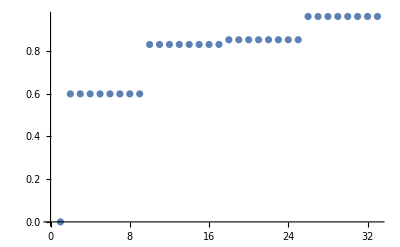

```mathematica
ListPlot[{0,0.5981703991651317,0.598214826944756,0.5982148297018578,0.5982252145175162,0.5982960697798091,0.5983261065400106,0.5983280740545044,0.5983448039840161,0.8292309920575744,0.8292396923334724,0.8293155603128334,0.8293221118419474,0.8293352185197325,0.8293398571625205,0.8294060075548508,0.8294135043270199,0.851208917985852,0.8512116301560783,0.8512125877158317,0.8512192932752722,0.8512598978259504,0.8512613749011415,0.8512694901589171,0.8512761204182897,0.9599666291265199,0.959972310913824,0.9599893830073493,0.95999380709471,0.9600463326377001,0.9600578251568429,0.9601128336695062,0.9601160721676741}]
```

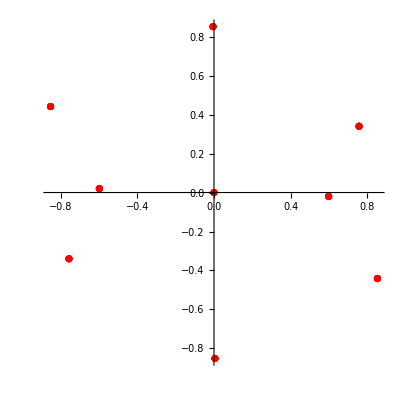

```mathematica
ComplexListPlot[{-2.556347987196246*^10+1.322502507902935*^10 ⅈ,-2.556335204753981*^10+1.3229071938402687*^10 ⅈ,-2.556037779141277*^10+1.3225071184696737*^10 ⅈ,-2.5559654850048874*^10+1.322795252716244*^10 ⅈ,-2.2680944753529114*^10-1.0190812406732197*^10 ⅈ,-2.2678953555848602*^10-1.0188079500315033*^10 ⅈ,-2.267800522059724*^10-1.019196729991772*^10 ⅈ,-2.26755262299621*^10-1.0189521514859804*^10 ⅈ,-1.7927621831698864*^10+5.930090709421259*^8 ⅈ,-1.7927433163751156*^10+5.969157370330483*^8 ⅈ,-1.7924193908226795*^10+5.939454197301772*^8 ⅈ,-1.792409989287638*^10+5.967783644092511*^8 ⅈ,-1.4986147758076283*^8+2.5518164909780746*^10 ⅈ,-1.4935763667089012*^8+2.552018257676041*^10 ⅈ,-1.4801782604379615*^8+2.5518285688062164*^10 ⅈ,-1.4762139255403438*^8+2.5519750612176647*^10 ⅈ,-1.39282636252236*^-110-1.3928263625223596*^-110 ⅈ,-1.39282636252236*^-110+1.39282636252236*^-110 ⅈ,1.3928263625223593*^-110+1.3928263625223602*^-110 ⅈ,1.3928263625223596*^-110-1.39282636252236*^-110 ⅈ,1.472801056270533*^8-2.5519708301756878*^10 ⅈ,1.4816276653520152*^8-2.551825613952172*^10 ⅈ,1.490510685584255*^8-2.5519985595524605*^10 ⅈ,1.496809528532527*^8-2.5518477018062584*^10 ⅈ,1.7922876316707344*^10-5.934910651091715*^8 ⅈ,1.7924398550042034*^10-5.971640227996275*^8 ⅈ,1.7926647930302124*^10-5.93429495373555*^8 ⅈ,1.792800389340032*^10-5.966188128627485*^8 ⅈ,2.267586056613966*^10+1.0189413838473282*^10 ⅈ,2.2677824663160557*^10+1.019202981498945*^10 ⅈ,2.2678960601900215*^10+1.0188543111651423*^10 ⅈ,2.268070993275276*^10+1.0190786654259245*^10 ⅈ,2.5559692502297905*^10-1.322816833453921*^10 ⅈ,2.5560463882941505*^10-1.3225275460590412*^10 ⅈ,2.5562986058405018*^10-1.322522977480058*^10 ⅈ,2.5563428737228283*^10-1.3228712499789227*^10 ⅈ}/(2.997925*10^10)//Chop,PlotRange->All,PlotStyle->Red]
```

```mathematica
FullSimplify[Tr[Gij]]
```

-2.63523×10^125+(5.86418×10^104-3.6299×10^62 ⅈ) r^2-(3.26239×10^83+3.6299×10^62 ⅈ) r^4-3.6299×10^62 r^6+(8.07761×10^41+4.49378×10^20 ⅈ) r^8-4.49378×10^20 r^10+r^2 Sin[t0]^2 (8.79628×10^104-(9.78718×10^83+3.6299×10^62 ⅈ) r^2-(7.2598×10^62-8.07761×10^41 ⅈ) r^4+(2.0194×10^42+8.98755×10^20 ⅈ) r^6-(1.34813×10^21+0.5 ⅈ) r^8+r^2 ((-6.52478×10^83+3.6299×10^62 ⅈ)-(4.03881×10^41-3.6299×10^62 ⅈ) r^2+8.07761×10^41 r^4-(8.98755×10^20+8.98755×10^20 ⅈ) r^6+(0.+0.5 ⅈ) r^8) Sin[t0]^2+r^4 (-3.6299×10^62+(8.07761×10^41-4.03881×10^41 ⅈ) r^2-4.49378×10^20 r^4) Sin[t0]^4+r^6 ((1.21164×10^42-8.98755×10^20 ⅈ)-(1.34813×10^21-0.5 ⅈ) r^2-(0.+0.5 ⅈ) r^4) Sin[t0]^6-(8.98755×10^20-0.5 ⅈ) r^8 Sin[t0]^8)

```mathematica
1/2 (-((-1+c^2-r^2) (c^10-c^6 (-1+r^2)-c^8 (1+r^2)-r^6 (1+r^2)+c^4 r^2 (ⅈ+ⅈ r^2+r^4)+c^2 (-1+(3+ⅈ) r^2+r^4-(1-ⅈ) r^6-r^8)))+r^2 Sin[t0]^2 (c^2 (5-2 c^2-2 c^6+3 c^8)+(-2 ⅈ+(9+4 ⅈ) c^2+ⅈ c^4-(2+ⅈ) c^6-3 c^8) r^2+(-ⅈ+2 c^2+(1+2 ⅈ) c^4-2 c^6) r^4+(-2-(1-2 ⅈ) c^2+5 c^4) r^6-((2+ⅈ)+3 c^2) r^8+r^2 (-5-2 c^8-(2+ⅈ) r^2+ⅈ c^6 ((1+ⅈ)+r^2)+ⅈ r^4 ((3+ⅈ)+(1+ⅈ) r^2+r^4)+c^4 (-ⅈ-(1+ⅈ) r^2+2 r^4)+c^2 (7+2 r^2+(2-2 ⅈ) r^4-(2+2 ⅈ) r^6)) Sin[t0]^2-r^4 ((1+ⅈ)+c^6+2 r^2+r^4+c^4 (-2-(2-ⅈ) r^2)+c^2 (1+ⅈ r^2+r^4)) Sin[t0]^4+r^6 (1+3 c^4+ⅈ r^2-ⅈ r^4-c^2 ((4+2 ⅈ)+3 r^2)) Sin[t0]^6+(1+ⅈ) (1-(1-ⅈ) c^2) r^8 Sin[t0]^8))/.t0->0/.c->2.997925*10^10
```

-1/2 (8.98755×10^20-r^2) (5.86418×10^104-7.2598×10^62 (-1+r^2)-6.52478×10^83 (1+r^2)-r^6 (1+r^2)+8.07761×10^41 r^2 (ⅈ+ⅈ r^2+r^4)+8.98755×10^20 (-1+(3+ⅈ) r^2+r^4-(1-ⅈ) r^6-r^8))

```mathematica
r/.Solve[-1/2 (8.987554305625*^20-r^2) (5.864184662240476*^104-7.259798765124243*^62 (-1+r^2)-6.524783564946346*^83 (1+r^2)-r^6 (1+r^2)+8.077613239655849*^41 r^2 (ⅈ+ⅈ r^2+r^4)+8.987554305625*^20 (-1+(3+ⅈ) r^2+r^4-(1-ⅈ) r^6-r^8))==1,r]
```

{-2.99793×10^10,-2.99793×10^10,-2.59628×10^10+1.49896×10^10 ⅈ,-2.59628×10^10-1.49896×10^10 ⅈ,0.-2.99793×10^10 ⅈ,0.+2.99793×10^10 ⅈ,2.59628×10^10-1.49896×10^10 ⅈ,2.59628×10^10+1.49896×10^10 ⅈ,2.99792×10^10,2.99792×10^10}

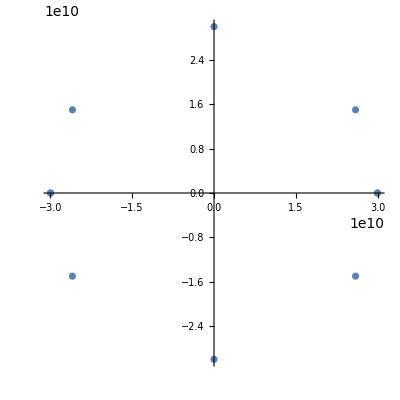

```mathematica
ComplexListPlot[{-2.997925*^10,-2.997925*^10,-2.5962792086404633*^10+1.4989624999999994*^10 ⅈ,-2.5962792086404633*^10-1.4989625*^10 ⅈ,0.-2.997925*^10 ⅈ,0.+2.997925*^10 ⅈ,2.5962792086404633*^10-1.4989624999999998*^10 ⅈ,2.5962792086404633*^10+1.4989625*^10 ⅈ,2.9979249999999996*^10,2.9979249999999996*^10}]
```

```mathematica
N[Eigenvalues[Gij/.r->c/.t0->0/.c->2.997925*10^10]]
```

{3.75767×10^109-5.86418×10^104 ⅈ,3.26239×10^83+5.86418×10^104 ⅈ,4.65199×10^67+6.52478×10^83 ⅈ,0.}

```mathematica
Abs[{5.721241081193138*^109-5.864184662218338*^104 ⅈ,-5.721241081193137*^109+5.864184662240477*^104 ⅈ,-6.365737426045269*^88+6.524783564946345*^83 ⅈ,0.}]/(2.997925*10^10)^2
```

{6.36574×10^88,6.36574×10^88,7.08284×10^67,0.}

```mathematica
{6.36573742637966*^88,6.365737426379658*^88,7.082836119716753*^67,0.}
```

{6.36574×10^88,6.36574×10^88,7.08284×10^67,0.}

```mathematica
{5.7212410814936725*^109,5.721241081493671*^109,6.365737426379658*^88,0.}/(6.365737426379658*^88)
```

{8.98755×10^20,8.98755×10^20,1.,0.}

```mathematica
{8.987554305625003*^20,8.987554305625*^20,1.,0.}/(2.997925*10^10)^2
```

{1.,1.,1.11265×10^-21,0.}

```mathematica
Abs[{5.721241081193138*^109-5.864184662218338*^104 ⅈ,-5.721241081193137*^109+5.864184662240477*^104 ⅈ,-6.365737426045269*^88+6.524783564946345*^83 ⅈ,0.}]/(2.997925*10^10)^4
```

{7.08284×10^67,7.08284×10^67,7.88072×10^46,0.}

```mathematica
Abs[{5.721241081193138*^109-5.864184662218338*^104 ⅈ,-5.721241081193137*^109+5.864184662240477*^104 ⅈ,-6.365737426045269*^88+6.524783564946345*^83 ⅈ,0.}]/(2.997925*10^10)^8
```

{8.76848×10^25,8.76848×10^25,97562.4,0.}

```mathematica
{8.768476416950265*^25,8.768476416950264*^25,97562.43043185148,0.}/(8.768476416950264*^25)
```

{1.,1.,1.11265×10^-21,0.}

```mathematica
Abs[{5.721241081193138*^109-5.864184662218338*^104 ⅈ,-5.721241081193137*^109+5.864184662240477*^104 ⅈ,-6.365737426045269*^88+6.524783564946345*^83 ⅈ,0.}]/(8.768476416950264*^25*(2.997925*10^10)^2)
```

{7.2598×10^62,7.2598×10^62,8.07761×10^41,0.}

```mathematica
N[Eigenvalues[Gij/.r->c/.t0->Pi/2/.c->2.997925*10^10]]/(2.997925*10^10)^2
```

{1.17284×10^105+5.86418×10^104 ⅈ,-1.17284×10^105-5.86418×10^104 ⅈ,-1.17284×10^105-5.86418×10^104 ⅈ,-1.30496×10^84-6.52478×10^83 ⅈ}

```mathematica
{-1.172836932448096*^105-5.864184662240481*^104 ⅈ,1.1728369324480956*^105+5.864184662240478*^104 ⅈ,-1.1728369324480956*^105-5.864184662240474*^104 ⅈ,-1.304956712989269*^84-6.524783564946345*^83 ⅈ}/(7.082836119716753*^67)
```

{-1.65589×10^37-8.27943×10^36 ⅈ,1.65589×10^37+8.27943×10^36 ⅈ,-1.65589×10^37-8.27943×10^36 ⅈ,-1.84242×10^16-9.21211×10^15 ⅈ}

```mathematica
Log[Abs[Join[{-1.172836932448096*^105-5.864184662240481*^104 ⅈ,1.1728369324480956*^105+5.864184662240478*^104 ⅈ,-1.1728369324480956*^105-5.864184662240474*^104 ⅈ,-1.304956712989269*^84-6.524783564946345*^83 ⅈ},{6.36573742637966*^88,6.365737426379658*^88,7.082836119716753*^67,0.}]/(7.082836119716753*^67)]]
```

{85.8116,85.8116,85.8116,37.564,48.2475,48.2475,0.,Indeterminate}

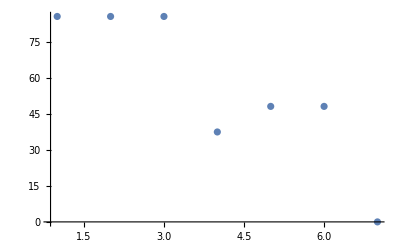

```mathematica
ListPlot[Log[Abs[Join[{-1.172836932448096*^105-5.864184662240481*^104 ⅈ,1.1728369324480956*^105+5.864184662240478*^104 ⅈ,-1.1728369324480956*^105-5.864184662240474*^104 ⅈ,-1.304956712989269*^84-6.524783564946345*^83 ⅈ},{6.36573742637966*^88,6.365737426379658*^88,7.082836119716753*^67,0.}]/(7.082836119716753*^67)]],PlotRange->All]
```

```mathematica
(-1.304956712989269*^84-6.524783564946345*^83 ⅈ)/(7.082836119716753*^67)
```

-1.84242×10^16-9.21211×10^15 ⅈ

```mathematica
(*mass of the observable  universe*)
```

```mathematica
(7.082836119716753*^67)/(4*10^57)
```

1.77071×10^10

```mathematica
Abs[Join[{-1.172836932448096*^105-5.864184662240481*^104 ⅈ,1.1728369324480956*^105+5.864184662240478*^104 ⅈ,-1.1728369324480956*^105-5.864184662240474*^104 ⅈ,-1.304956712989269*^84-6.524783564946345*^83 ⅈ},{6.36573742637966*^88,6.365737426379658*^88,7.082836119716753*^67,0.}]]/(4*10^57)
```

{3.27818×10^47,3.27818×10^47,3.27818×10^47,3.64746×10^26,1.59143×10^31,1.59143×10^31,1.77071×10^10,0.}

```mathematica
(*mass of the observable  universewith dark energy*)
```

```mathematica
(4*10^57)/0.78+(4*10^57)/(1-0.78)
```

2.331×10^58

```mathematica
4.80325*10^(-10)*Abs[Join[{-1.172836932448096*^105-5.864184662240481*^104 ⅈ,1.1728369324480956*^105+5.864184662240478*^104 ⅈ,-1.1728369324480956*^105-5.864184662240474*^104 ⅈ,-1.304956712989269*^84-6.524783564946345*^83 ⅈ},{6.36573742637966*^88,6.365737426379658*^88,7.082836119716753*^67,0.}]]/(2.331002331002331*^58)
```

{2.702×10^37,2.702×10^37,2.702×10^37,3.00638×10^16,1.31172×10^21,1.31172×10^21,1.45949,0.}

```mathematica
1/%
```

Power::infy: Infinite expression 1/0. encountered.

{3.70096×10^-38,3.70096×10^-38,3.70096×10^-38,3.32626×10^-17,7.62358×10^-22,7.62358×10^-22,0.685173,ComplexInfinity}